# International Interaction Game

## Quantum-like Signorino’s Backward Induction Model

Quantum Extension of Signorino’s International Interaction Game Model

### Quantum-like Backward Induction Functions

```mathematica
(*Quantum Backward Induction Functions*)q10quantum[theta1_,theta2_,U2War1_,U2Cap2_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l2*U2War1];
denominator=Exp[l2*U2War1]+Exp[l2*U2Cap2];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]];

notq10quantum[theta1_,theta2_,U2War1_,U2Cap2_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l2*U2War1];
denominator=Exp[l2*U2War1]+Exp[l2*U2Cap2];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]];

q11quantum[theta1_,theta2_,U2War1_,U2Cap2_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l2*U2War1];
denominator=Exp[l2*U2War1]+Exp[l2*U2Cap2];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]];

notq11quantum[theta1_,theta2_,U2War1_,U2Cap2_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l2*U2War1];
denominator=Exp[l2*U2War1]+Exp[l2*U2Cap2];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]];

p8quantum[theta1_,theta2_,U1War2_,U1Cap1_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l1*U1War2];
denominator=Exp[l1*U1War2]+Exp[l1*U1Cap1];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]]

notp8quantum[theta1_,theta2_,U1War2_,U1Cap1_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l1*U1War2];
denominator=Exp[l1*U1War2]+Exp[l1*U1Cap1];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]];

p12quantum[theta1_,theta2_,U1War2_,U1Cap1_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l1*U1War2];
denominator=Exp[l1*U1War2]+Exp[l1*U1Cap1];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]];

notp12quantum[theta1_,theta2_,U1War2_,U1Cap1_,l1_:1,l2_:1]:=Module[{numerator,denominator,exponentialFactor},numerator=Exp[l1*U1War2];
denominator=Exp[l1*U1War2]+Exp[l1*U1Cap1];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]];

q9quantum[theta1_,theta2_,U1War2_,U1Cap1_,U2War2_,U2Cap1_,U2Nego_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP2N12,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];

(* UP2N12=p12val*Conjugate[p12val]*U2War2+notp12val*Conjugate[notp12val]*U2Cap1; *)

UP2N12=p12val*Conjugate[p12val]*U2War2+notp12val*Conjugate[notp12val]*U2Cap1 + 2 p12val  Sqrt[U2War2] notp12val Sqrt[U2Cap1] Cos[theta1 - theta2];

numerator=Exp[l2*UP2N12];
denominator=Exp[l2*UP2N12]+Exp[l2*U2Nego];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]];

notq9quantum[theta1_,theta2_,U1War2_,U1Cap1_,U2War2_,U2Cap1_,U2Nego_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP2N12,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];

(* UP2N12=p12val*Conjugate[p12val]*U2War2+notp12val*Conjugate[notp12val]*U2Cap1; *)
UP2N12=p12val*Conjugate[p12val]*U2War2+notp12val*Conjugate[notp12val]*U2Cap1 + 2 p12val  Sqrt[U2War2] notp12val Sqrt[U2Cap1] Cos[theta1 - theta2];

numerator=Exp[l2*UP2N12];
denominator=Exp[l2*UP2N12]+Exp[l2*U2Nego];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]];

p7quantum[theta1_,theta2_,U1War1_,U1Cap2_,U2War1_,U2Cap2_,U1Nego_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP1N11,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];

(* UP1N11=q11val*Conjugate[q11val]*U1War1+notq11val*Conjugate[notq11val]*U1Cap2; *)
UP1N11=q11val*Conjugate[q11val]*U1War1+notq11val*Conjugate[notq11val]*U1Cap2 + 2 q11val Sqrt[U1War1] notq11val Sqrt[U1Cap2] Cos[theta1 - theta2];

numerator=Exp[l1*UP1N11];
denominator=Exp[l1*UP1N11]+Exp[l1*U1Nego];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]];

notp7quantum[theta1_,theta2_,U1War1_,U1Cap2_,U2War1_,U2Cap2_,U1Nego_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP1N11,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];

(* UP1N11=q11val*Conjugate[q11val]*U1War1+notq11val*Conjugate[notq11val]*U1Cap2; *)
UP1N11=q11val*Conjugate[q11val]*U1War1+notq11val*Conjugate[notq11val]*U1Cap2 + 2 q11val Sqrt[U1War1] notq11val Sqrt[U1Cap2] Cos[theta1 - theta2];

numerator=Exp[l1*UP1N11];
denominator=Exp[l1*UP1N11]+Exp[l1*U1Nego];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]];

q6quantum[theta1_,theta2_,U1War1_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,l1_:1,l2_:1]:=Module[{p8val,p7val,notp7val,notp8val,UP2N8,q11val,notq11val,U2N11,UP2N7,numerator,denominator,exponentialFactor},p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];

(* UP2N8=p8val*Conjugate[p8val]*U2War2+notp8val*Conjugate[notp8val]*U2Cap1; *)
UP2N8=p8val*Conjugate[p8val]*U2War2+notp8val*Conjugate[notp8val]*U2Cap1 + 2 p8val Sqrt[U2War2] notp8val Sqrt[U2Cap1] Cos[theta1-theta2];

q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];

(* U2N11=q11val*Conjugate[q11val]*U2War1+notq11val*Conjugate[notq11val]*U2Cap2;*)
U2N11=q11val*Conjugate[q11val]*U2War1+notq11val*Conjugate[notq11val]*U2Cap2 + 2 q11val Sqrt[U2War1]  notq11val Sqrt[U2Cap2] Cos[theta1 - theta2];

p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];

(* UP2N7=p7val*Conjugate[p7val]*U2N11+notp7val*Conjugate[notp7val]*U2Nego; *)
UP2N7=p7val*Conjugate[p7val]*U2N11+notp7val*Conjugate[notp7val]*U2Nego + 2 p7val Sqrt[U2N11] notp7val Sqrt[U2Nego] Cos[theta1 - theta2] ;

numerator=Exp[l2*UP2N8];
denominator=Exp[l2*UP2N8]+Exp[l2*UP2N7];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]];

notq6quantum[theta1_,theta2_,U1War1_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,l1_:1,l2_:1]:=Module[{p8val,p7val,notp7val,notp8val,UP2N8,q11val,notq11val,U2N11,UP2N7,numerator,denominator,exponentialFactor},p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];

(* UP2N8=p8val*Conjugate[p8val]*U2War2+notp8val*Conjugate[notp8val]*U2Cap1;*)
UP2N8=p8val*Conjugate[p8val]*U2War2+notp8val*Conjugate[notp8val]*U2Cap1 + 2 p8val Sqrt[U2War2] notp8val Sqrt[U2Cap1] Cos[theta1-theta2];

q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];

(* U2N11=q11val*Conjugate[q11val]*U2War1+notq11val*Conjugate[notq11val]*U2Cap2; *)
U2N11=q11val*Conjugate[q11val]*U2War1+notq11val*Conjugate[notq11val]*U2Cap2 + 2 q11val Sqrt[U2War1]  notq11val Sqrt[U2Cap2] Cos[theta1 - theta2];

p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];

(* UP2N7=p7val*Conjugate[p7val]*U2N11+notp7val*Conjugate[notp7val]*U2Nego; *)
UP2N7=p7val*Conjugate[p7val]*U2N11+notp7val*Conjugate[notp7val]*U2Nego + 2 p7val Sqrt[U2N11] notp7val Sqrt[U2Nego] Cos[theta1 - theta2] ;

numerator=Exp[l2*UP2N8];
denominator=Exp[l2*UP2N8]+Exp[l2*UP2N7];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]];

p5quantum[theta1_,theta2_,U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP1N12,q10val,notq10val,UP1N10,q9val,notq9val,UP1N9,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];

(* UP1N12=p12val*Conjugate[p12val]*U1War2+notp12val*Conjugate[notp12val]*U1Cap1; *)
UP1N12=p12val*Conjugate[p12val]*U1War2+notp12val*Conjugate[notp12val]*U1Cap1 + 2 p12val Sqrt[U1War2]  notp12val Sqrt[U1War2] Cos[theta1-theta2];

q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];

(* UP1N10=q10val*Conjugate[q10val]*U1War1+notq10val*Conjugate[notq10val]*U1Cap2; *)
UP1N10=q10val*Conjugate[q10val]*U1War1+notq10val*Conjugate[notq10val]*U1Cap2 + 2 q10val Sqrt[U1War1] notq10val Sqrt[U1Cap2] Cos[theta1 - theta2];

q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];

(* UP1N9=q9val*Conjugate[q9val]*UP1N12+notq9val*Conjugate[notq9val]*U1Nego; *)
UP1N9=q9val*Conjugate[q9val]*UP1N12+notq9val*Conjugate[notq9val]*U1Nego + 2 q9val Sqrt[UP1N12] notq9val Sqrt[U1Nego] Cos[theta1 - theta2] ;  

numerator=Exp[l1*UP1N10];
denominator=Exp[l1*UP1N10]+Exp[l1*UP1N9];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]];

notp5quantum[theta1_,theta2_,U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP1N12,q10val,notq10val,UP1N10,q9val,notq9val,UP1N9,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];

(* UP1N12=p12val*Conjugate[p12val]*U1War2+notp12val*Conjugate[notp12val]*U1Cap1; *)
UP1N12=p12val*Conjugate[p12val]*U1War2+notp12val*Conjugate[notp12val]*U1Cap1 + 2 p12val Sqrt[U1War2]  notp12val Sqrt[U1War2] Cos[theta1-theta2];

q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];

(* UP1N10=q10val*Conjugate[q10val]*U1War1+notq10val*Conjugate[notq10val]*U1Cap2; *)
UP1N10=q10val*Conjugate[q10val]*U1War1+notq10val*Conjugate[notq10val]*U1Cap2 + 2 q10val Sqrt[U1War1] notq10val Sqrt[U1Cap2] Cos[theta1 - theta2];

q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];

(* UP1N9=q9val*Conjugate[q9val]*UP1N12+notq9val*Conjugate[notq9val]*U1Nego; *)
UP1N9=q9val*Conjugate[q9val]*UP1N12+notq9val*Conjugate[notq9val]*U1Nego + 2 q9val Sqrt[UP1N12] notq9val Sqrt[U1Nego] Cos[theta1 - theta2] ;  

numerator=Exp[l1*UP1N10];
denominator=Exp[l1*UP1N10]+Exp[l1*UP1N9];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]
];

p4quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP1N11,p8val,notp8val,UP1N8,p7val,notp7val,UP1N7,q6val,notq6val,UP1N6,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];

(* UP1N11=q11val*Conjugate[q11val]*U1War1+notq11val*Conjugate[notq11val]*U1Cap2; *)
UP1N11=q11val*Conjugate[q11val]*U1War1+notq11val*Conjugate[notq11val]*U1Cap2 + 2 q11val Sqrt[U1War1] notq11val Sqrt[U1Cap2] Cos[ theta1 - theta2]; 

p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];

(* UP1N8=p8val*Conjugate[p8val]*U1War2+notp8val*Conjugate[notp8val]*U1Cap1; *)

UP1N8=p8val*Conjugate[p8val]*U1War2+notp8val*Conjugate[notp8val]*U1Cap1 + 2 p8val Sqrt[U1War2] notp8val Sqrt[U1Cap1] Cos[theta1 - theta2];

p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];

(* UP1N7=p7val*Conjugate[p7val]*UP1N11+notp7val*Conjugate[notp7val]*U1Nego; *)
UP1N7=p7val*Conjugate[p7val]*UP1N11+notp7val*Conjugate[notp7val]*U1Nego + 2  p7val Sqrt[UP1N11] notp7val Sqrt[U1Nego] Cos[theta1 - theta2];

q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];

(* UP1N6=q6val*Conjugate[q6val]*UP1N8+notq6val*Conjugate[notq6val]*UP1N7; *)
UP1N6=q6val*Conjugate[q6val]*UP1N8+notq6val*Conjugate[notq6val]*UP1N7 + 2q6val Sqrt[UP1N8] notq6val Sqrt[UP1N7] Cos[theta1 - theta2] ;

numerator=Exp[l1*UP1N6];
denominator=Exp[l1*UP1N6]+Exp[l1*U1Acq1];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]
];

notp4quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP1N11,p8val,notp8val,UP1N8,p7val,notp7val,UP1N7,q6val,notq6val,UP1N6,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];

(* UP1N11=q11val*Conjugate[q11val]*U1War1+notq11val*Conjugate[notq11val]*U1Cap2; *)
UP1N11=q11val*Conjugate[q11val]*U1War1+notq11val*Conjugate[notq11val]*U1Cap2 + 2 q11val Sqrt[U1War1] notq11val Sqrt[U1Cap2] Cos[ theta1 - theta2]; 

p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];

(* UP1N8=p8val*Conjugate[p8val]*U1War2+notp8val*Conjugate[notp8val]*U1Cap1; *)
UP1N8=p8val*Conjugate[p8val]*U1War2+notp8val*Conjugate[notp8val]*U1Cap1 + 2 p8val Sqrt[U1War2] notp8val Sqrt[U1Cap1] Cos[theta1 - theta2];

p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];

(* UP1N7=p7val*Conjugate[p7val]*UP1N11+notp7val*Conjugate[notp7val]*U1Nego; *) 
UP1N7=p7val*Conjugate[p7val]*UP1N11+notp7val*Conjugate[notp7val]*U1Nego + 2  p7val Sqrt[UP1N11] notp7val Sqrt[U1Nego] Cos[theta1 - theta2];

q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];

(* UP1N6=q6val*Conjugate[q6val]*UP1N8+notq6val*Conjugate[notq6val]*UP1N7; *)
UP1N6=q6val*Conjugate[q6val]*UP1N8+notq6val*Conjugate[notq6val]*UP1N7 + 2q6val Sqrt[UP1N8] notq6val Sqrt[UP1N7] Cos[theta1 - theta2] ;

numerator=Exp[l1*UP1N6];
denominator=Exp[l1*UP1N6]+Exp[l1*U1Acq1];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]
];

q3quantum[theta1_,theta2_,U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_,U2Acq2_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP2N12,q10val,notq10val,UP2N10,q9val,notq9val,UP2N9,p5val,notp5val,UP2N5,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];

(* UP2N12=p12val*Conjugate[p12val]*U2War2+notp12val*Conjugate[notp12val]*U2Cap1; *)
UP2N12=p12val*Conjugate[p12val]*U2War2+notp12val*Conjugate[notp12val]*U2Cap1 + 2 p12val Sqrt[p12val] notp12val Sqrt[notp12val] Cos[theta1 - theta2];

q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];

(* UP2N10=q10val*Conjugate[q10val]*U2War1+notq10val*Conjugate[notq10val]*U2Cap2; *)
UP2N10=q10val*Conjugate[q10val]*U2War1+notq10val*Conjugate[notq10val]*U2Cap2 + 2 q10val Sqrt[U2War1] notq10val Sqrt[U2Cap2] Cos[theta1 - theta2];

q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];

(* UP2N9=q9val*Conjugate[q9val]*UP2N12+notq9val*Conjugate[notq9val]*U2Nego; *)
UP2N9=q9val*Conjugate[q9val]*UP2N12+notq9val*Conjugate[notq9val]*U2Nego + 2 q9val Sqrt[UP2N12] notq9val Sqrt[U2Nego] Cos[theta1 - theta2];

p5val=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notp5val=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];

(* UP2N5=p5val*Conjugate[p5val]*UP2N10+notp5val*Conjugate[notp5val]*UP2N9; *)
UP2N5=p5val*Conjugate[p5val]*UP2N10+notp5val*Conjugate[notp5val]*UP2N9 + 2 p5val Sqrt[UP2N10] notp5val Sqrt[UP2N9] Cos[theta1 - theta2]; 

numerator=Exp[l2*UP2N5];
denominator=Exp[l2*UP2N5]+Exp[l2*U2Acq2];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]
];

notq3quantum[theta1_,theta2_,U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_,U2Acq2_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP2N12,q10val,notq10val,UP2N10,q9val,notq9val,UP2N9,p5val,notp5val,UP2N5,numerator,denominator,exponentialFactor},p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];

(* UP2N12=p12val*Conjugate[p12val]*U2War2+notp12val*Conjugate[notp12val]*U2Cap1; *)
UP2N12=p12val*Conjugate[p12val]*U2War2+notp12val*Conjugate[notp12val]*U2Cap1 + 2 p12val Sqrt[p12val] notp12val Sqrt[notp12val] Cos[theta1 - theta2];

q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];

(* UP2N10=q10val*Conjugate[q10val]*U2War1+notq10val*Conjugate[notq10val]*U2Cap2; *)
UP2N10=q10val*Conjugate[q10val]*U2War1+notq10val*Conjugate[notq10val]*U2Cap2 + 2 q10val Sqrt[U2War1] notq10val Sqrt[U2Cap2] Cos[theta1 - theta2];

q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];

(* UP2N9=q9val*Conjugate[q9val]*UP2N12+notq9val*Conjugate[notq9val]*U2Nego; *)
UP2N9=q9val*Conjugate[q9val]*UP2N12+notq9val*Conjugate[notq9val]*U2Nego + 2 q9val Sqrt[UP2N12] notq9val Sqrt[U2Nego] Cos[theta1 - theta2];

p5val=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notp5val=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];

(* UP2N5=p5val*Conjugate[p5val]*UP2N10+notp5val*Conjugate[notp5val]*UP2N9; *)
UP2N5=p5val*Conjugate[p5val]*UP2N10+notp5val*Conjugate[notp5val]*UP2N9 + 2 p5val Sqrt[UP2N10] notp5val Sqrt[UP2N9] Cos[theta1 - theta2]; 

numerator=Exp[l2*UP2N5];
denominator=Exp[l2*UP2N5]+Exp[l2*U2Acq2];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]
];

q2quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U2SQ_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP2N11,p7val,notp7val,UP2N7,p8val,notp8val,UP2N8,q6val,notq6val,UP2N6,p4val,notp4val,UP2N4,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];

(* UP2N11=q11val*Conjugate[q11val]*U2War1+notq11val*Conjugate[notq11val]*U2Cap2; *)
UP2N11=q11val*Conjugate[q11val]*U2War1+notq11val*Conjugate[notq11val]*U2Cap2 + 2 q11val Sqrt[U2War1] notq11val Sqrt[U2Cap2] Cos[theta1 - theta2];

p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];

(* UP2N7=p7val*Conjugate[p7val]*UP2N11+notp7val*Conjugate[notp7val]*U2Nego; *)
UP2N7=p7val*Conjugate[p7val]*UP2N11+notp7val*Conjugate[notp7val]*U2Nego + 2 p7val Sqrt[UP2N11] notp7val Sqrt[U2Nego] Cos[theta1 - theta2];

p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];

(* UP2N8=p8val*Conjugate[p8val]*U2War2+notp8val*Conjugate[notp8val]*U2Cap1; *)
UP2N8=p8val*Conjugate[p8val]*U2War2+notp8val*Conjugate[notp8val]*U2Cap1 + 2 p8val Sqrt[U2War2] notp8val Sqrt[U2Cap1] Cos[theta1 - theta2];

q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];

(* UP2N6=q6val*Conjugate[q6val]*UP2N8+notq6val*Conjugate[notq6val]*UP2N7; *)
UP2N6=q6val*Conjugate[q6val]*UP2N8+notq6val*Conjugate[notq6val]*UP2N7 + 2 q6val Sqrt[UP2N8] notq6val Sqrt[UP2N7] Cos[theta1 - theta2];

p4val=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notp4val=notp4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];

(* UP2N4=p4val*Conjugate[p4val]*UP2N6+notp4val*Conjugate[notp4val]*U2Acq1; *)
UP2N4=p4val*Conjugate[p4val]*UP2N6+notp4val*Conjugate[notp4val]*U2Acq1 + 2 p4val Sqrt[UP2N6] notp4val Sqrt[U2Acq1] Cos[theta1 - theta2];

numerator=Exp[l2*UP2N4];
denominator=Exp[l2*UP2N4]+Exp[l2*U2SQ];
exponentialFactor=I*theta2;
Sqrt[numerator/denominator]*Exp[exponentialFactor]];

notq2quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U2SQ_,l1_:1,l2_:1]:=Module[{q11val,notq11val,UP2N11,p7val,notp7val,UP2N7,p8val,notp8val,UP2N8,q6val,notq6val,UP2N6,p4val,notp4val,UP2N4,numerator,denominator,exponentialFactor},q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];

(* UP2N11=q11val*Conjugate[q11val]*U2War1+notq11val*Conjugate[notq11val]*U2Cap2; *)
UP2N11=q11val*Conjugate[q11val]*U2War1+notq11val*Conjugate[notq11val]*U2Cap2 + 2 q11val Sqrt[U2War1] notq11val Sqrt[U2Cap2] Cos[theta1 - theta2];

p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];

(* UP2N7=p7val*Conjugate[p7val]*UP2N11+notp7val*Conjugate[notp7val]*U2Nego; *)
UP2N7=p7val*Conjugate[p7val]*UP2N11+notp7val*Conjugate[notp7val]*U2Nego + 2 p7val Sqrt[UP2N11] notp7val Sqrt[U2Nego] Cos[theta1 - theta2];

p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];

(* UP2N8=p8val*Conjugate[p8val]*U2War2+notp8val*Conjugate[notp8val]*U2Cap1; *)
UP2N8=p8val*Conjugate[p8val]*U2War2+notp8val*Conjugate[notp8val]*U2Cap1 + 2 p8val Sqrt[U2War2] notp8val Sqrt[U2Cap1] Cos[theta1 - theta2];

q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];

(* UP2N6=q6val*Conjugate[q6val]*UP2N8+notq6val*Conjugate[notq6val]*UP2N7; *)
UP2N6=q6val*Conjugate[q6val]*UP2N8+notq6val*Conjugate[notq6val]*UP2N7 + 2 q6val Sqrt[UP2N8] notq6val Sqrt[UP2N7] Cos[theta1 - theta2];

p4val=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notp4val=notp4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];

(* UP2N4=p4val*Conjugate[p4val]*UP2N6+notp4val*Conjugate[notp4val]*U2Acq1; *)
UP2N4=p4val*Conjugate[p4val]*UP2N6+notp4val*Conjugate[notp4val]*U2Acq1 + 2 p4val Sqrt[UP2N6] notp4val Sqrt[U2Acq1] Cos[theta1 - theta2];

numerator=Exp[l2*UP2N4];
denominator=Exp[l2*UP2N4]+Exp[l2*U2SQ];
exponentialFactor=I*theta2;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]
];

p1quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=
Module[{p12val,notp12val,UP1N12,q11val,notq11val,UP1N11,q9val,notq9val,UP1N9,p7val,notp7val,UP1N7,p8val,notp8val,UP1N8,q10val,notq10val,UP1N10,q6val,notq6val,UP1N6,p5val,notp5val,UP1N5,p4val,notp4val,UP1N4,q3val,notq3val,UP1N3,q2val,notq2val,UP1N2,numerator,denominator,exponentialFactor},

p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];

(* UP1N12=p12val*Conjugate[p12val]*U1War1+notp12val*Conjugate[notp12val]*U1Cap1; *)
UP1N12=p12val*Conjugate[p12val]*U1War1+notp12val*Conjugate[notp12val]*U1Cap1 + 2 p12val Sqrt[U1War1] notp12val Sqrt[U1Cap1] Cos[theta1 - theta2] ;

q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];

(* UP1N11=q11val*Conjugate[q11val]*U1War1+notq11val*Conjugate[notq11val]*U1Cap2; *)
UP1N11=q11val*Conjugate[q11val]*U1War1+notq11val*Conjugate[notq11val]*U1Cap2 + 2 q11val Sqrt[U1War1] notq11val Sqrt[U1Cap2] Cos[theta1 - theta2];

q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];

(* UP1N9=q9val*Conjugate[q9val]*UP1N12+notq9val*Conjugate[notq9val]*U1Nego; *)
UP1N9=q9val*Conjugate[q9val]*UP1N12+notq9val*Conjugate[notq9val]*U1Nego + 2 q9val Sqrt[UP1N12] notq9val Sqrt[U1Nego] Cos[theta1 - theta2] ;

p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];

(* UP1N7=p7val*Conjugate[p7val]*UP1N11+notp7val*Conjugate[notp7val]*U1Nego; *)
UP1N7=p7val*Conjugate[p7val]*UP1N11+notp7val*Conjugate[notp7val]*U1Nego + 2 p7val Sqrt[UP1N11] notp7val Sqrt[U1Nego] Cos[theta1 - theta2];

p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];

(* UP1N8=p8val*Conjugate[p8val]*U1War2+notp8val*Conjugate[notp8val]*U1Cap1; *)
UP1N8=p8val*Conjugate[p8val]*U1War2+notp8val*Conjugate[notp8val]*U1Cap1 + 2 p8val Sqrt[U1War2]notp8val Sqrt[U1Cap1]Cos[theta1 - theta2] ;

q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];

(* UP1N10=q10val*Conjugate[q10val]*U1War1+notq10val*Conjugate[notq10val]*U1Cap2; *)
UP1N10=q10val*Conjugate[q10val]*U1War1+notq10val*Conjugate[notq10val]*U1Cap2 + 2 q10val Sqrt[U1War1] notq10val Sqrt[U1Cap2] Cos[theta1 - theta2];

q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];

(* UP1N6=q6val*Conjugate[q6val]*UP1N8+notq6val*Conjugate[notq6val]*UP1N7; *)
 UP1N6=q6val*Conjugate[q6val]*UP1N8+notq6val*Conjugate[notq6val]*UP1N7 + 2 q6val Sqrt[UP1N8]  notq6val Sqrt[UP1N7] Cos[theta1 - theta2];

p5val=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notp5val=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];

(* UP1N5=p5val*Conjugate[p5val]*UP1N10+notp5val*Conjugate[notp5val]*UP1N9; *)
UP1N5=p5val*Conjugate[p5val]*UP1N10+notp5val*Conjugate[notp5val]*UP1N9 + 2 p5val Sqrt[UP1N10]notp5val Sqrt[UP1N9] Cos[theta1 - theta2];

p4val=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notp4val=notp4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];

(* UP1N4=p4val*Conjugate[p4val]*UP1N6+notp4val*Conjugate[notp4val]*U1Acq1; *)
UP1N4=p4val*Conjugate[p4val]*UP1N6+notp4val*Conjugate[notp4val]*U1Acq1 + 2 p4val Sqrt[UP1N6] notp4val Sqrt[U1Acq1] Cos[theta1 - theta2];

q3val=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
notq3val=notq3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];

(* UP1N3=q3val*Conjugate[q3val]*UP1N5+notq3val*Conjugate[notq3val]*U1Acq2; *)
UP1N3=q3val*Conjugate[q3val]*UP1N5+notq3val*Conjugate[notq3val]*U1Acq2 + 2 q3val Sqrt[UP1N5] notq3val Sqrt[U1Acq2] Cos[theta1 - theta2];
 
q2val=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
notq2val=notq2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];

(* UP1N2=q2val*Conjugate[q2val]*UP1N4+notq2val*Conjugate[notq2val]*U1SQ; *)
UP1N2=q2val*Conjugate[q2val]*UP1N4+notq2val*Conjugate[notq2val]*U1SQ + 2 q2val Sqrt[UP1N4] notq2val Sqrt[U1SQ] Cos[theta1 - theta2] ;

numerator=Exp[l1*UP1N3];
denominator=Exp[l1*UP1N3]+Exp[l1*UP1N2];
exponentialFactor=I*theta1;
Sqrt[numerator/denominator]*Exp[exponentialFactor]
];

notp1quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{p12val,notp12val,UP1N12,q11val,notq11val,UP1N11,q9val,notq9val,UP1N9,p7val,notp7val,UP1N7,p8val,notp8val,UP1N8,q10val,notq10val,UP1N10,q6val,notq6val,UP1N6,p5val,notp5val,UP1N5,p4val,notp4val,UP1N4,q3val,notq3val,UP1N3,q2val,notq2val,UP1N2,numerator,denominator,exponentialFactor},

p12val=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp12val=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];

(* UP1N12=p12val*Conjugate[p12val]*U1War1+notp12val*Conjugate[notp12val]*U1Cap1;*)
UP1N12=p12val*Conjugate[p12val]*U1War1+notp12val*Conjugate[notp12val]*U1Cap1 + 2 p12val Sqrt[U1War1] notp12val Sqrt[U1Cap1] Cos[theta1 - theta2] ;

q11val=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq11val=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];

(* UP1N11=q11val*Conjugate[q11val]*U1War1+notq11val*Conjugate[notq11val]*U1Cap2;*)
UP1N11=q11val*Conjugate[q11val]*U1War1+notq11val*Conjugate[notq11val]*U1Cap2 + 2 q11val Sqrt[U1War1] notq11val Sqrt[U1Cap2] Cos[theta1 - theta2];

q9val=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
notq9val=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];

(* UP1N9=q9val*Conjugate[q9val]*UP1N12+notq9val*Conjugate[notq9val]*U1Nego; *)
UP1N9=q9val*Conjugate[q9val]*UP1N12+notq9val*Conjugate[notq9val]*U1Nego + 2 q9val Sqrt[UP1N12] notq9val Sqrt[U1Nego] Cos[theta1 - theta2] ;

p7val=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
notp7val=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];

(* UP1N7=p7val*Conjugate[p7val]*UP1N11+notp7val*Conjugate[notp7val]*U1Nego; *)
UP1N7=p7val*Conjugate[p7val]*UP1N11+notp7val*Conjugate[notp7val]*U1Nego + 2 p7val Sqrt[UP1N11] notp7val Sqrt[U1Nego] Cos[theta1 - theta2];

p8val=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
notp8val=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];

(* UP1N8=p8val*Conjugate[p8val]*U1War2+notp8val*Conjugate[notp8val]*U1Cap1; *)
UP1N8=p8val*Conjugate[p8val]*U1War2+notp8val*Conjugate[notp8val]*U1Cap1 + 2 p8val Sqrt[U1War2]notp8val Sqrt[U1Cap1]Cos[theta1 - theta2] ;

q10val=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
notq10val=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];

(* UP1N10=q10val*Conjugate[q10val]*U1War1+notq10val*Conjugate[notq10val]*U1Cap2;*)
UP1N10=q10val*Conjugate[q10val]*U1War1+notq10val*Conjugate[notq10val]*U1Cap2 + 2 q10val Sqrt[U1War1] notq10val Sqrt[U1Cap2] Cos[theta1 - theta2];

q6val=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
notq6val=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];

(* UP1N6=q6val*Conjugate[q6val]*UP1N8+notq6val*Conjugate[notq6val]*UP1N7; *)
UP1N6=q6val*Conjugate[q6val]*UP1N8+notq6val*Conjugate[notq6val]*UP1N7 + 2 q6val Sqrt[UP1N8]  notq6val Sqrt[UP1N7] Cos[theta1 - theta2];

p5val=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
notp5val=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];

(* UP1N5=p5val*Conjugate[p5val]*UP1N10+notp5val*Conjugate[notp5val]*UP1N9; *)
UP1N5=p5val*Conjugate[p5val]*UP1N10+notp5val*Conjugate[notp5val]*UP1N9 + 2 p5val Sqrt[UP1N10]notp5val Sqrt[UP1N9] Cos[theta1 - theta2];

p4val=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
notp4val=notp4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];

(* UP1N4=p4val*Conjugate[p4val]*UP1N6+notp4val*Conjugate[notp4val]*U1Acq1; *)
UP1N4=p4val*Conjugate[p4val]*UP1N6+notp4val*Conjugate[notp4val]*U1Acq1 + 2 p4val Sqrt[UP1N6] notp4val Sqrt[U1Acq1] Cos[theta1 - theta2];

q3val=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
notq3val=notq3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];

(* UP1N3=q3val*Conjugate[q3val]*UP1N5+notq3val*Conjugate[notq3val]*U1Acq2; *)
UP1N3=q3val*Conjugate[q3val]*UP1N5+notq3val*Conjugate[notq3val]*U1Acq2 + 2 q3val Sqrt[UP1N5] notq3val Sqrt[U1Acq2] Cos[theta1 - theta2];

q2val=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
notq2val=notq2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];

(* UP1N2=q2val*Conjugate[q2val]*UP1N4+notq2val*Conjugate[notq2val]*U1SQ; *)
UP1N2=q2val*Conjugate[q2val]*UP1N4+notq2val*Conjugate[notq2val]*U1SQ + 2 q2val Sqrt[UP1N4] notq2val Sqrt[U1SQ] Cos[theta1 - theta2] ;

numerator=Exp[l1*UP1N3];
denominator=Exp[l1*UP1N3]+Exp[l1*UP1N2];
exponentialFactor=I*theta1;
Sqrt[1-numerator/denominator]*Exp[exponentialFactor]
];
```

### Outcome Functions

```mathematica
SQquantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{notp1,notq2,res},notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
notq2=notq2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
Re[(notp1*notq2) Conjugate[(notp1*notq2)]]
];

ACQ1quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{notp1,q2,notp4},
notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];

q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
notp4=notp4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
Re[(notp1*q2*notp4) Conjugate[(notp1*q2*notp4)]]
];

ACQ2quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{p1,notq3},p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
notq3=notq3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
Re[(p1*notq3)Conjugate[(p1*notq3)] ]
];

NEGOquantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{p1,notp1,q2,q3,p4,notp5,notq6,notp7,notq9, classp1,classnotp1,classq2,classq3,classp4,classnotp5,classnotq6,classnotp7,classnotq9, pathClass1, pathClass2},p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
classp1 = p1 Conjugate[p1];

notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
classnotp1 = notp1 Conjugate[notp1];

q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
classq2 = q2 Conjugate[q2];

q3=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
classq3 = q3 Conjugate[q3];

p4=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
classp4=p4 Conjugate[p4];

notp5=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
classnotp5 = notp5 Conjugate[notp5];
 
notq6=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
classnotq6 = notq6 Conjugate[notq6];

notp7=notp7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
classnotp7 = notp7 Conjugate[notp7];

notq9=notq9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
classnotq9 = notq9 Conjugate[notq9];

pathClass1 = classnotp1*classq2*classp4*classnotq6*classnotp7;
pathClass2 = classp1*classq3*classnotp5*classnotq9;

Re[pathClass1 + pathClass2 + 2 Sqrt[pathClass1 + pathClass2] Cos[theta1 - theta2]]
];

CAP1quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{notp1,q2,p4,q6,notp8,p1,q3,notp5,q9,notp12,classnotp1,classq2,classp4,classq6,classnotp8,classp1,classq3,classnotp5,classq9,classnotp12,pathClass1,pathClass2},

notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
classnotp1 = notp1 Conjugate[notp1];

q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
classq2 = q2 Conjugate[q2];

p4=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
classp4 = p4 Conjugate[p4];

q6=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
classq6 = q6 Conjugate[q6];

notp8=notp8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
classnotp8 = notp8 Conjugate[notp8];

p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
classp1 = p1 Conjugate[p1];

q3=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
classq3 = q3 Conjugate[q3];

notp5=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
classnotp5 = notp5 Conjugate[notp5];

q9=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
classq9 = q9 Conjugate[q9];

notp12=notp12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
classnotp12 = notp12  Conjugate[notp12];

pathClass1=classnotp1*classq2*classp4*classq6*classnotp8;
pathClass2=classp1*classq3*classnotp5*classq9*classnotp12;

Re[pathClass1 + pathClass2 + 2 Sqrt[pathClass1 + pathClass2] Cos[theta1 - theta2]]
];

CAP2quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=
Module[{notp1,q2,p4,notq6,p7,notq11,p1,q3,p5,notq10,classnotp1,classq2,classp4,classnotq6,classp7,classnotq11,classp1,classq3,classp5,classnotq10, pathClass1, pathClass2},

notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
classnotp1 = notp1 Conjugate[notp1];

q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
classq2 = q2 Conjugate[q2];

p4=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
classp4 = p4 Conjugate[p4];

notq6=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
classnotq6 = notq6 Conjugate[notq6];

p7=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
classp7 = p7 Conjugate[p7];

notq11=notq11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
classnotq11 = notq11 Conjugate[notq11];

p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
classp1 = p1 Conjugate[p1];

q3=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
classq3 = q3 Conjugate[q3];

p5=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
classp5 = p5 Conjugate[p5];

notq10=notq10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
classnotq10 = notq10 Conjugate[notq10];

pathClass1 = classnotp1*classq2*classp4*classnotq6*classp7*classnotq11;
pathClass2 = classp1*classq3*classp5*classnotq10;

Re[pathClass1 + pathClass2 + 2 Sqrt[pathClass1 + pathClass2] Cos[theta1 - theta2]]
];

WAR1quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{notp1,p1,q2,p4,notq6,p7,q11,q3,q10,p5, classnotp1,classp1,classq2,classp4,classnotq6,classp7,classq11,classq3,classq10,classp5,pathClass1,pathClass2},

notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
classnotp1 = notp1 Conjugate[notp1];

p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
classp1 = p1 Conjugate[p1];

q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
classq2 = q2 Conjugate[q2];

p4=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
classp4 = p4 Conjugate[p4];

notq6=notq6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
classnotq6=notq6 Conjugate[notq6];

p7=p7quantum[theta1,theta2,U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,l1,l2];
classp7 = p7 Conjugate[p7];

q11=q11quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
classq11 = q11 Conjugate[q11];

q3=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
classq3 = q3 Conjugate[q3];

q10=q10quantum[theta1,theta2,U2War1,U2Cap2,l1,l2];
classq10 = q10 Conjugate[q10];

p5=p5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
classp5 = p5 Conjugate[p5];

pathClass1 = classnotp1*classq2*classp4*classnotq6*classp7*classq11;
pathClass2 = classp1*classq3*classp5*classq10;

Re[pathClass1 + pathClass2 + 2 Sqrt[pathClass1 + pathClass2] Cos[theta1 - theta2]]
];

WAR2quantum[theta1_,theta2_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,l1_:1,l2_:1]:=Module[{notp1,p1,q2,p4,q6,p8,q3,notp5,q9,p12, classnotp1,classp1,classq2,classp4,classq6,classp8,classq3,classnotp5,classq9,classp12, pathClass1, pathClass2},

notp1=notp1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
classnotp1 = notp1 Conjugate[notp1];

p1=p1quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,l1,l2];
classp1 = p1 Conjugate[p1];

q2=q2quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,l1,l2];
classq2 = q2 Conjugate[q2];

p4=p4quantum[theta1,theta2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,l1,l2];
classp4 = p4 Conjugate[p4];

q6=q6quantum[theta1,theta2,U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,l1,l2];
classq6 = q6 Conjugate[q6];

p8=p8quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
classp8 = p8 Conjugate[p8];

q3=q3quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,l1,l2];
classq3 = q3 Conjugate[q3];

notp5=notp5quantum[theta1,theta2,U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,l1,l2];
classnotp5 = notp5 Conjugate[notp5];

q9=q9quantum[theta1,theta2,U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,l1,l2];
classq9 = q9 Conjugate[q9];

p12=p12quantum[theta1,theta2,U1War2,U1Cap1,l1,l2];
classp12 = p12 Conjugate[p12];

pathClass1 = classnotp1*classq2*classp4*classq6*classp8;
pathClass2 = classp1*classq3*classnotp5*classq9*classp12;

Re[pathClass1 + pathClass2 + 2 Sqrt[pathClass1 + pathClass2] Cos[theta1 - theta2]]
];
```

### Aux Functions

#### calculateQuantumOutcome

```mathematica
calculateQuantumOutcome[data_,rowIndex_Integer,theta1_:0,theta2_:0,l1_:1,l2_:1]:=Module[{utils,quantumProbabilities,finalProbabilities,outcomes,outcomeProbs,maxVal,maxOutcomes,prediction,roundedProbs},

utils=extractUtilities[data,rowIndex];
If[utils===$Failed,
Return[$Failed]];

(*Compute quantum probability amplitudes*)
quantumProbabilities=
Quiet[{
ACQ1quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],
utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],
utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],
utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],

ACQ2quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],

CAP1quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],

CAP2quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],

NEGOquantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],

SQquantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],
utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],
utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],
utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],

WAR1quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2],

WAR2quantum[theta1,theta2,utils["U1War2"],utils["U1Cap1"],utils["U1Cap2"],utils["U2War2"],utils["U2Cap1"],utils["U1War1"],utils["U2War1"],utils["U2Cap2"],utils["U1Nego"],utils["U2Nego"],utils["U1Acq1"],utils["U2Acq1"],utils["U1Acq2"],utils["U2Acq2"],utils["U1SQ"],utils["U2SQ"],l1,l2]
}];

(* Normalize probabilities *)
finalProbabilities=quantumProbabilities/Total[quantumProbabilities];

outcomes={"ACQ1","ACQ2","CAP1","CAP2","NEGO","SQ","WAR1","WAR2"};

(*Create outcome probabilities association for prediction*)
outcomeProbs=Association[MapThread[Rule,{outcomes,finalProbabilities}]];

(*Round probabilities to 4 decimal places for comparison*)
roundedProbs=Association[#->Round[outcomeProbs[#],0.0001]&/@Keys[outcomeProbs]];
maxVal=Max[Values[roundedProbs]];
maxOutcomes=Keys[Select[roundedProbs,#==maxVal&]];

(*Randomly select one if there are ties*)
prediction=RandomChoice[maxOutcomes];

Association[

"ACQ1"->finalProbabilities[[1]],
"ACQ2"->finalProbabilities[[2]],
"CAP1"->finalProbabilities[[3]],
"CAP2"->finalProbabilities[[4]],
"NEGO"->finalProbabilities[[5]],
"SQ"->finalProbabilities[[6]],
"WAR1"->finalProbabilities[[7]],
"WAR2"->finalProbabilities[[8]],
"prediction"->prediction,
"groundtruth"->utils["groundtruth"],
"utilities"->utils,
"theta1"->theta1,
"theta2"->theta2,
"l1"->l1,"l2"->l2,
"total"->Total[finalProbabilities]]]
```

#### getFirstNEntries

```mathematica
getFirstNEntries[resultAllData_,N_Integer]:=Module[{extractedEntries},
(*Input validation*)
If[!ListQ[resultAllData],
Print["Error: resultAllData must be a list"];
Return[$Failed]
];

If[N<=0,
Print["Error: N must be a positive integer"];
Return[$Failed]
];

If[Length[resultAllData]==0,
Print["Warning: resultAllData is empty"];
Return[{}]
];

(*Extract only the specified components from each entry*)
extractedEntries=
Table[Module[{entry,utils},
entry=resultAllData[[i]];
utils=If[KeyExistsQ[entry,"utilities"],entry["utilities"],Association[]];

Association[
"SQ"->If[KeyExistsQ[entry,"SQ"],Round[entry["SQ"],0.0001],0],
"ACQ1"->If[KeyExistsQ[entry,"ACQ1"],Round[entry["ACQ1"],0.0001],0],
"ACQ2"->If[KeyExistsQ[entry,"ACQ2"],Round[entry["ACQ2"],0.0001],0],
"NEGO"->If[KeyExistsQ[entry,"NEGO"],Round[entry["NEGO"],0.0001],0],
"CAP1"->If[KeyExistsQ[entry,"CAP1"],Round[entry["CAP1"],0.0001],0],
"CAP2"->If[KeyExistsQ[entry,"CAP2"],Round[entry["CAP2"],0.0001],0],
"WAR1"->If[KeyExistsQ[entry,"WAR1"],Round[entry["WAR1"],0.0001],0],
"WAR2"->If[KeyExistsQ[entry,"WAR2"],Round[entry["WAR2"],0.0001],0],
"prediction"->If[KeyExistsQ[entry,"prediction"],entry["prediction"],"UNKNOWN"],
"groundtruth"->If[KeyExistsQ[entry,"groundtruth"],entry["groundtruth"],"UNKNOWN"],
"Agent1"->If[KeyExistsQ[utils,"Agent1"],utils["Agent1"],"UNKNOWN"],
"Agent2"->If[KeyExistsQ[utils,"Agent2"],utils["Agent2"],"UNKNOWN"]]
],{i,Min[N,Length[resultAllData]]}
];

(*Return extracted entries with informative message*)
If[N>=Length[resultAllData],
Print["Note: Requested ",N," entries but only ",Length[resultAllData]," available. Returning all entries with extracted components."];
Return[extractedEntries],
Print["Returning first ",N," entries out of ",Length[resultAllData]," total entries with extracted components."];
Return[extractedEntries]]]
```

#### processQuantumDataset

```mathematica
(*Process Quantum Dataset*)
processQuantumDataset[data_,theta1_:0,theta2_:0,l1_:1,l2_:1]:=Module[{results,i},
If[data===$Failed,
Print["Error: Invalid data passed to processQuantumDataset"];
Return[{}]
];

Print["Processing ",data["nrows"]," rows with quantum model..."];
Print["Parameters: θ1=",theta1,", θ2=",theta2,", λ1=",l1,", λ2=",l2];
results={};
Do[
Module[{result},
If[Mod[i,50]==0,
Print["Processing row ",i,"/",data["nrows"]]
];
result=calculateQuantumOutcome[data,i,theta1,theta2,l1,l2];
If[result=!=$Failed,
AppendTo[results,result],
Print["Warning: Failed to process row ",i]
]
],{i,1,data["nrows"]}
];
Print["Successfully processed ",Length[results]," out of ",data["nrows"]," rows"];
results
];
```

#### calculateQuantumAccuracy

```mathematica
calculateQuantumAccuracy[results_]:=Module[{predictions,groundTruths,res},
If[Length[results]==0,
Print["Warning: No results to calculate accuracy from"];
Return[0]
];

res=extractPredictionsAndGroundtruth[results];

If[Length[res["predictions"]]==0,
Print["Warning: No valid predictions found"];
Return[0]
];

predictions=res["predictions"];
groundTruths=res["groundtruth"];

N[Count[MapThread[Equal,{predictions,groundTruths}],True]/Length[results]]
];
```

#### plotQuantumConfusionMatrix

```mathematica
plotQuantumConfusionMatrix[results_,theta1_:0,theta2_:0,l1_:1,l2_:1,title_:"Quantum Confusion Matrix"]:=Module[{predictions,groundTruths,outcomes,confusionData,accuracy,predTruth,res},

If[Length[results]==0,
Print["Warning: No results provided for confusion matrix"];
Return[Null]
];

res=extractPredictionsAndGroundtruth[results];
predictions=res["predictions"];
groundTruths=res["groundtruth"];

accuracy=calculateQuantumAccuracy[results];
outcomes={"ACQ1","ACQ2","CAP1","CAP2","NEGO","SQ","WAR1", "WAR2"};
confusionData=Table[Count[MapThread[List,{groundTruths,predictions}],{actualOutcome,predictedOutcome}],{actualOutcome,outcomes},{predictedOutcome,outcomes}];
Print[Style[title,16,Bold]];
Print[Style["θ1 = "<>ToString[theta1]<>" θ2 = "<>ToString[theta2]<>" λ1 = "<>ToString[l1]<>" λ2 = "<>ToString[l2]<>" | Accuracy = "<>ToString[N[accuracy]],14]];
Print[""];
Grid[Prepend[MapThread[Prepend,{confusionData,outcomes}],Prepend[outcomes,Style["Actual \\ Predicted",Bold]]],Frame->All,Alignment->Center,Background->{None,{LightBlue,None}},ItemStyle->{Automatic,{Bold,Automatic}},Spacings->{2,1},FrameStyle->Thick,Dividers->{{2->Thick},{2->Thick}}]]
```

#### loadData

```mathematica
loadData[filename_String]:=Module[{rawData,headers,dataRows,groundtruth,utilityData,cleanedData,requiredColumns,missingColumns},

Print["Loading CSV file: ",filename];
rawData=Import[filename,"CSV"];

If[Head[rawData]=!=List||Length[rawData]<2,
Print["Error: Could not load CSV file or file is empty"];
Return[$Failed]
];

headers=First[rawData];
dataRows=Rest[rawData];

Print["Loaded ",Length[dataRows]," rows with ",Length[headers]," columns"];
cleanedData=Map[Function[row,Map[Function[cell,If[NumericQ[cell],cell,If[StringQ[cell]&&StringMatchQ[cell,NumberString],ToExpression[cell],cell]]],row]],dataRows];
groundtruth=cleanedData[[All,-1]];

utilityData=Association[Table[headers[[i]]->cleanedData[[All,i]],{i,Length[headers]}]];

requiredColumns={"wrTu1ac1","wrTu1ac2","wrTu1cp1","wrTu1cp2","wrTu1neg","wrTu1sq","wrTu1wr1","wrTu1wr2","wrTu2ac1","wrTu2ac2","wrTu2cp1","wrTu2cp2","wrTu2neg","wrTu2sq","wrTu2wr1","wrTu2wr2"};

missingColumns=Select[requiredColumns,!KeyExistsQ[utilityData,#]&];
If[Length[missingColumns]>0,
Print["Warning: Missing required columns: ",missingColumns];
];

Association[
"groundtruth"->groundtruth,
"data"->utilityData,
"nrows"->Length[cleanedData],
"headers"->headers,
"filename"->filename]
]
```

#### extractUtilities

```mathematica
extractUtilities[data_,rowIndex_Integer]:=Module[{row,utils},
If[rowIndex<1||rowIndex>data["nrows"],
Print["Error: Row index ",rowIndex," out of range [1, ",data["nrows"],"]"];
Return[$Failed]
];

row=data["data"];
utils=Association[];

(*Player 1 utilities*)
utils["U1Acq1"]=If[KeyExistsQ[row,"wrTu1ac1"]&&NumericQ[row["wrTu1ac1"][[rowIndex]]],row["wrTu1ac1"][[rowIndex]],0.0];
utils["U1Acq2"]=If[KeyExistsQ[row,"wrTu1ac2"]&&NumericQ[row["wrTu1ac2"][[rowIndex]]],row["wrTu1ac2"][[rowIndex]],0.0];
utils["U1Cap1"]=If[KeyExistsQ[row,"wrTu1cp1"]&&NumericQ[row["wrTu1cp1"][[rowIndex]]],row["wrTu1cp1"][[rowIndex]],0.0];
utils["U1Cap2"]=If[KeyExistsQ[row,"wrTu1cp2"]&&NumericQ[row["wrTu1cp2"][[rowIndex]]],row["wrTu1cp2"][[rowIndex]],0.0];
utils["U1Nego"]=If[KeyExistsQ[row,"wrTu1neg"]&&NumericQ[row["wrTu1neg"][[rowIndex]]],row["wrTu1neg"][[rowIndex]],0.0];
utils["U1SQ"]=If[KeyExistsQ[row,"wrTu1sq"]&&NumericQ[row["wrTu1sq"][[rowIndex]]],row["wrTu1sq"][[rowIndex]],0.0];
utils["U1War1"]=If[KeyExistsQ[row,"wrTu1wr1"]&&NumericQ[row["wrTu1wr1"][[rowIndex]]],row["wrTu1wr1"][[rowIndex]],0.0];
utils["U1War2"]=If[KeyExistsQ[row,"wrTu1wr2"]&&NumericQ[row["wrTu1wr2"][[rowIndex]]],row["wrTu1wr2"][[rowIndex]],0.0];

(*Player 2 utilities*)
utils["U2Acq1"]=If[KeyExistsQ[row,"wrTu2ac1"]&&NumericQ[row["wrTu2ac1"][[rowIndex]]],row["wrTu2ac1"][[rowIndex]],0.0];
utils["U2Acq2"]=If[KeyExistsQ[row,"wrTu2ac2"]&&NumericQ[row["wrTu2ac2"][[rowIndex]]],row["wrTu2ac2"][[rowIndex]],0.0];
utils["U2Cap1"]=If[KeyExistsQ[row,"wrTu2cp1"]&&NumericQ[row["wrTu2cp1"][[rowIndex]]],row["wrTu2cp1"][[rowIndex]],0.0];
utils["U2Cap2"]=If[KeyExistsQ[row,"wrTu2cp2"]&&NumericQ[row["wrTu2cp2"][[rowIndex]]],row["wrTu2cp2"][[rowIndex]],0.0];
utils["U2Nego"]=If[KeyExistsQ[row,"wrTu2neg"]&&NumericQ[row["wrTu2neg"][[rowIndex]]],row["wrTu2neg"][[rowIndex]],0.0];
utils["U2SQ"]=If[KeyExistsQ[row,"wrTu2sq"]&&NumericQ[row["wrTu2sq"][[rowIndex]]],row["wrTu2sq"][[rowIndex]],0.0];
utils["U2War1"]=If[KeyExistsQ[row,"wrTu2wr1"]&&NumericQ[row["wrTu2wr1"][[rowIndex]]],row["wrTu2wr1"][[rowIndex]],0.0];
utils["U2War2"]=If[KeyExistsQ[row,"wrTu2wr2"]&&NumericQ[row["wrTu2wr2"][[rowIndex]]],row["wrTu2wr2"][[rowIndex]],0.0];

utils["Agent1"]=If[KeyExistsQ[row,"ISOShNm1"],row["ISOShNm1"][[rowIndex]],"Unknown"];
utils["Agent2"]=If[KeyExistsQ[row,"ISOShNm2"],row["ISOShNm2"][[rowIndex]],"Unknown"];

(*Additional information*)
utils["groundtruth"]=data["groundtruth"][[rowIndex]];
utils["ccode1"]=If[KeyExistsQ[row,"ccode1"]&&NumericQ[row["ccode1"][[rowIndex]]],row["ccode1"][[rowIndex]],0];
utils["ccode2"]=If[KeyExistsQ[row,"ccode2"]&&NumericQ[row["ccode2"][[rowIndex]]],row["ccode2"][[rowIndex]],0];
utils["year"]=If[KeyExistsQ[row,"year"]&&NumericQ[row["year"][[rowIndex]]],row["year"][[rowIndex]],0];
utils
];
```

#### extractPredictionsAndGroundtruth

```mathematica
extractPredictionsAndGroundtruth[results_]:=Module[{predictions,groundTruth,outcomes},
outcomes={"ACQ1","ACQ2","CAP1","CAP2","NEGO","SQ","WAR1", "WAR2"};
predictions=
Table[
Module[{outcomeProbs,maxVal,maxOutcome},
outcomeProbs=
Association[
"ACQ1"->If[KeyExistsQ[results[[i]],"ACQ1"]&&NumericQ[results[[i]]["ACQ1"]],results[[i]]["ACQ1"],"ERROR"],
"ACQ2"->If[KeyExistsQ[results[[i]],"ACQ2"]&&NumericQ[results[[i]]["ACQ2"]],results[[i]]["ACQ2"],"ERROR"],
"CAP1"->If[KeyExistsQ[results[[i]],"CAP1"]&&NumericQ[results[[i]]["CAP1"]],results[[i]]["CAP1"],"ERROR"],
"CAP2"->If[KeyExistsQ[results[[i]],"CAP2"]&&NumericQ[results[[i]]["CAP2"]],results[[i]]["CAP2"],"ERROR"],
"NEGO"->If[KeyExistsQ[results[[i]],"NEGO"]&&NumericQ[results[[i]]["NEGO"]],results[[i]]["NEGO"],"ERROR"],
"SQ"->If[KeyExistsQ[results[[i]],"SQ"]&&NumericQ[results[[i]]["SQ"]],results[[i]]["SQ"],"ERROR"],
"WAR1"->If[KeyExistsQ[results[[i]],"WAR1"]&&NumericQ[results[[i]]["WAR1"]],results[[i]]["WAR1"],"ERROR"],
"WAR2"->If[KeyExistsQ[results[[i]],"WAR2"]&&NumericQ[results[[i]]["WAR2"]],results[[i]]["WAR2"],"ERROR"]
];

(*Find outcome with maximum probability*)
maxVal=Max[Values[outcomeProbs]];
maxOutcome=First[Keys[Select[outcomeProbs,#==maxVal&]]];
maxOutcome],{i,Length[results]}];

groundTruth=Table[If[KeyExistsQ[results[[i]],"groundtruth"],results[[i]]["groundtruth"],"UNKNOWN"],{i,Length[results]}];
Association[
"predictions"->predictions,
"groundtruth"->groundTruth]
];
```

### Optimization Functions

```mathematica
(*Grid Search Function for Optimal Theta Parameters*)
gridSearchQuantumThetas[data_,theta1Range_List,theta2Range_List,l1_:1,l2_:1,verbose_:True]:=Module[{results,bestAccuracy,bestTheta1,bestTheta2,totalCombinations,currentCombination,startTime,gridResults,theta1Values,theta2Values},

(*Input validation*)
If[data===$Failed||!KeyExistsQ[data,"nrows"],
Print["Error: Invalid data provided"];
Return[$Failed]
];

(*Extract theta values from ranges*)
theta1Values=theta1Range;
theta2Values=theta2Range;
totalCombinations=Length[theta1Values]*Length[theta2Values];
currentCombination=0;
bestAccuracy=0;
bestTheta1=First[theta1Values];
bestTheta2=First[theta2Values];

If[verbose,
Print["Starting grid search over ",totalCombinations," parameter combinations..."];
Print["Theta1 range: ",theta1Values];
Print["Theta2 range: ",theta2Values];
Print["Lambda1 = ",l1,", Lambda2 = ",l2];
Print["Dataset size: ",data["nrows"]," rows"];
Print[""];
];

startTime=AbsoluteTime[];
gridResults={};

(*Grid search loop*)
Do[
Module[{currentResults,currentAccuracy,elapsedTime,estimatedTotal,estimatedRemaining},

currentCombination++;
If[verbose&&Mod[currentCombination,Max[1,Floor[totalCombinations/20]]]==0,
elapsedTime=AbsoluteTime[]-startTime;
estimatedTotal=elapsedTime*totalCombinations/currentCombination;
estimatedRemaining=estimatedTotal-elapsedTime;
Print["Progress: ",currentCombination,"/",totalCombinations," (",N[100*currentCombination/totalCombinations,3],"%)"];
Print["Elapsed: ",N[elapsedTime/60,2]," min, Estimated remaining: ",N[estimatedRemaining/60,2]," min"];
Print["Current best: θ1=",bestTheta1,", θ2=",bestTheta2,", Accuracy=",N[bestAccuracy,4]];
Print[""];
];

(*Calculate results for current theta combination*)
currentResults=Quiet[processQuantumDataset[data,theta1,theta2,l1,l2]];
If[Length[currentResults]>0,
Print[Length[currentResults]];
currentAccuracy=calculateQuantumAccuracy[currentResults];

exportPath="D:\\home\\Documents\\Github\\quantum_international_interaction_game\\BN\\quantum_interaction_results_"<>"theta1_"<>ToString[N[theta1,3]]<>"_theta2_"<>ToString[N[theta2,3]]<>"_acc_"<>ToString[N[currentAccuracy,4]]<>".csv";

exportQuantumResultsToCSV[results,exportPath];

(*Store result*)
AppendTo[gridResults,
Association["theta1"->theta1,"theta2"->theta2,"accuracy"->currentAccuracy,"l1"->l1,"l2"->l2]
];

(*Update best parameters if current is better*)
If[currentAccuracy>bestAccuracy,
bestAccuracy=currentAccuracy;
bestTheta1=theta1;
bestTheta2=theta2;

If[verbose,
Print["New best found: θ1=",theta1,", θ2=",theta2,", Accuracy=",N[currentAccuracy,4]];
];
];,

(*Handle failed calculation*)
If[verbose,
Print["Warning: Failed to calculate results for θ1=",theta1,", θ2=",theta2];
];
AppendTo[gridResults,
Association["theta1"->theta1,"theta2"->theta2,"accuracy"->0,"l1"->l1,"l2"->l2,"failed"->True]
];
];
],
{theta1,theta1Values},{theta2,theta2Values}
];

If[verbose,
Print["Grid search completed!"];
Print["Total time: ",N[(AbsoluteTime[]-startTime)/60,2]," minutes"];
Print["Best parameters found:"];
Print["  θ1 = ",bestTheta1];
Print["  θ2 = ",bestTheta2];
Print["  Accuracy = ",N[bestAccuracy,4]];
Print[""];
];

(*Return comprehensive results*)
Association["bestTheta1"->bestTheta1,
"bestTheta2"->bestTheta2,
"bestAccuracy"->bestAccuracy,
"allResults"->gridResults,
"totalCombinations"->totalCombinations,
"l1"->l1,"l2"->l2]
]

(*Helper function to create parameter ranges*)
createThetaRange[min_,max_,steps_]:=
If[steps==1,
{min},
Range[min,max,(max-min)/(steps-1)]
]

(*Function to visualize grid search results*)
visualizeGridSearchResults[gridSearchResults_]:=Module[{validResults,heatmapData,theta1Values,theta2Values,accuracyMatrix,minAcc,maxAcc,tickLabels1,tickLabels2,theta1Ticks,theta2Ticks,bestIndex,plot},

(*Check if this is a proper grid search result structure*)If[!AssociationQ[gridSearchResults]||!KeyExistsQ[gridSearchResults,"allResults"],Print["Error: Input must be a grid search results Association with 'allResults' key"];
Print["Use gridSearchQuantumThetas[] to generate proper grid search results"];
Return[Null];
];

validResults=Select[gridSearchResults["allResults"],!KeyExistsQ[#,"failed"]&];
If[Length[validResults]==0,
Print["No valid results to visualize"];
Return[Null];
];
theta1Values=Sort[DeleteDuplicates[#["theta1"]&/@validResults]];
theta2Values=Sort[DeleteDuplicates[#["theta2"]&/@validResults]];

(*Create accuracy matrix for heatmap*)
accuracyMatrix=Table[
Module[{matchingResult},
matchingResult=SelectFirst[validResults,#["theta1"]==theta1&&#["theta2"]==theta2&];
If[matchingResult===Missing["NotFound"],
0,
matchingResult["accuracy"]
]
],{theta1,theta1Values},{theta2,theta2Values}
];

(*Calculate min/max for better color scaling*)
minAcc=Min[Flatten[accuracyMatrix]];
maxAcc=Max[Flatten[accuracyMatrix]];

(*Create proper tick labels*)
tickLabels1=Table[{i,NumberForm[N[theta1Values[[i]],3],{4,3}]},{i,Length[theta1Values]}];
tickLabels2=Table[{i,NumberForm[N[theta2Values[[i]],3],{4,3}]},{i,Length[theta2Values]}];

(*Find position of best result for highlighting*)
bestIndex=Position[accuracyMatrix,maxAcc];
Print[Style["Grid Search Results Visualization",16,Bold]];
Print[Style[StringJoin["Parameter Space: ",ToString[Length[theta1Values]]," × ",ToString[Length[theta2Values]]," = ",ToString[Length[validResults]]," combinations"],14]];
Print[Style[StringJoin["Best Parameters: θ₁ = ",ToString[NumberForm[N[gridSearchResults["bestTheta1"],4],{5,4}]],", θ₂ = ",ToString[NumberForm[N[gridSearchResults["bestTheta2"],4],{5,4}]]," → Accuracy = ",ToString[NumberForm[N[gridSearchResults["bestAccuracy"],4],{5,4}]]," (",ToString[NumberForm[100*N[gridSearchResults["bestAccuracy"]],{5,2}]],"%)"],14,RGBColor[0.1,0.5,0.1]]];
Print[Style[StringJoin["Accuracy Range: ",ToString[NumberForm[N[minAcc],{4,3}]]," - ",ToString[NumberForm[N[maxAcc],{4,3}]]],12,Gray]];
Print[""];

(*Create improved heatmap*)
plot=ArrayPlot[Transpose[accuracyMatrix],
(*Professional color scheme*)
ColorFunction->(Blend[{RGBColor[0.2,0.2,0.4],
(*Dark blue for low values*)
RGBColor[0.3,0.6,0.8],
(*Medium blue*)
RGBColor[0.9,0.9,0.3],
(*Yellow for medium values*)
RGBColor[0.9,0.6,0.1],
(*Orange*)
RGBColor[0.8,0.2,0.2]     
(*Red for high values*)},#]&),ColorFunctionScaling->True,

(*Proper labels and ticks*)
PlotLabel->Style["Parameter Optimization Heatmap",16,Bold],FrameLabel->{Style["θ₁ (Player 1 Quantum Phase)",14,Bold],Style["θ₂ (Player 2 Quantum Phase)",14,Bold]},

(*Custom ticks with actual parameter values*)
FrameTicks->{{tickLabels2,None},
(*Bottom ticks for theta2*)
{tickLabels1,None}  
 (*Left ticks for theta1*)
},(*Plot options*)
AspectRatio->Automatic,
ImageSize->{500,400},
Frame->True,
FrameStyle->Black,
PlotRangePadding->None,
(*Color bar legend*)PlotLegends->Placed[BarLegend[{Blend[{RGBColor[0.2,0.2,0.4],RGBColor[0.3,0.6,0.8],RGBColor[0.9,0.9,0.3],RGBColor[0.9,0.6,0.1],RGBColor[0.8,0.2,0.2]},#]&,{minAcc,maxAcc}},LegendLabel->Style["Accuracy",12,Bold],LegendMarkerSize->200],Right]];

(*Display summary statistics*)
Print[Style["Summary Statistics:",14,Bold]];
Print["• Mean Accuracy: ",NumberForm[Mean[Flatten[accuracyMatrix]],{4,3}]];
Print["• Standard Deviation: ",NumberForm[StandardDeviation[Flatten[accuracyMatrix]],{4,3}]];
Print["• Improvement over Random: ",NumberForm[100*(maxAcc-1/7),{4,2}],"% points"];
plot]

(*Function to get top N parameter combinations*)
getTopParameterCombinations[gridSearchResults_,n_:5]:=Module[{validResults,sortedResults},validResults=Select[gridSearchResults["allResults"],!KeyExistsQ[#,"failed"]&];
sortedResults=Reverse[SortBy[validResults,#["accuracy"]&]];
Take[sortedResults,Min[n,Length[sortedResults]]]]

(*For a focused search around your current parameters:*)
focusedSearchAroundCurrent[data_,currentTheta1_,currentTheta2_,rangeSize_:1.0,gridSize_:5]:=Module[{theta1Range,theta2Range,results},Print["Running focused search around θ1=",currentTheta1,", θ2=",currentTheta2];
theta1Range=createThetaRange[currentTheta1-rangeSize,currentTheta1+rangeSize,gridSize];
theta2Range=createThetaRange[currentTheta2-rangeSize,currentTheta2+rangeSize,gridSize];
Print["θ1 range: ",theta1Range];
Print["θ2 range: ",theta2Range];
results=gridSearchQuantumThetas[data,theta1Range,theta2Range,1,1,True];
Print["Focused search completed. Visualizing results..."];
visualizeGridSearchResults[results];
results]

(*Simple function to analyze current results *)analyzeCurrentResults[quantumResults_List]:=Module[{accuracy,sampleResult,theta1Val,theta2Val,predTruth},If[Length[quantumResults]==0,Print["No results to analyze"];
Return[$Failed];
];
(*Get sample result to extract theta values*)sampleResult=First[quantumResults];
theta1Val=sampleResult["theta1"];
theta2Val=sampleResult["theta2"];

(*Calculate accuracy*)
accuracy=calculateQuantumAccuracy[quantumResults];

(*Get predictions and ground truth*)predTruth=extractPredictionsAndGroundtruth[quantumResults];
Print["=== Quantum Model Analysis ==="];
Print["Parameters: θ1 = ",N[theta1Val,4]," (",theta1Val,")"];
Print["           θ2 = ",N[theta2Val,4]," (",theta2Val,")"];
Print["Total cases: ",Length[quantumResults]];
Print["Accuracy: ",N[accuracy,4]," (",N[100*accuracy,2],"%)"];
Print[""];

(*Show outcome distribution*)Module[{outcomes,counts},outcomes={"SQ","ACQ1","ACQ2","NEGO","CAP1","CAP2","WAR1","WAR2"};
counts=Table[Count[predTruth["predictions"],outcome],{outcome,outcomes}];
Print["Prediction distribution:"];
Do[If[counts[[i]]>0,Print["  ",outcomes[[i]],": ",counts[[i]]," (",N[100*counts[[i]]/Length[predTruth["predictions"]],1],"%)"]],{i,Length[outcomes]}];];
Print[""];

(*Show confusion matrix*)plotQuantumConfusionMatrix[quantumResults,theta1Val,theta2Val,1,1,"Current Quantum Model Results"];
Association["accuracy"->accuracy,"theta1"->theta1Val,"theta2"->theta2Val,"totalCases"->Length[quantumResults],"predictions"->predTruth["predictions"],"groundTruth"->predTruth["groundtruth"]]]
```

```mathematica
(*Function to process quantum interaction game results and save to CSV*)exportQuantumResultsToCSV[results_List,filename_String]:=Module[{processedData,headers,csvData,fullPath,exportSuccess},
(*Input validation*)
If[Length[results]==0,
Print["Error: No results to export"];
Return[$Failed]];

If[!StringQ[filename]||filename=="",
Print["Error: Invalid filename provided"];
Return[$Failed]
];
Print["Processing ",Length[results]," results for export..."];

(*Process each result entry*)
processedData=Table[processResultEntry[results[[i]],i],{i,Length[results]}];

(*Remove any failed entries*)
processedData=Select[processedData,#=!=$Failed&];
If[Length[processedData]==0,
Print["Error: No valid data to export"];
Return[$Failed]
];

(*Extract headers from first entry*)
headers=Keys[First[processedData]];

(*Convert to list format for CSV export*)
csvData=Prepend[Table[Values[processedData[[i]]],{i,Length[processedData]}],headers];
fullPath=If[StringEndsQ[filename,".csv"],filename,filename<>".csv"];

(*Export to CSV*)
exportSuccess=Quiet[Export[fullPath,csvData,"CSV"]];
If[exportSuccess=!=$Failed,
Print["Successfully exported ",Length[processedData]," results to: ",fullPath];
Print["File contains ",Length[headers]," columns and ",Length[processedData]," data rows"];
Return[fullPath],
Print["Error: Failed to export to ",fullPath];
Return[$Failed]]
]

(*Helper function to process individual result entry*)
processResultEntry[result_,rowIndex_Integer]:=Module[{processedEntry,utils},

(*Check if result is valid*)
If[!AssociationQ[result],
Print["Warning: Invalid result at index ",rowIndex];
Return[$Failed]];

(*Extract utilities if available*)
utils=If[KeyExistsQ[result,"utilities"],
result["utilities"],
Association[]
];

(*Build processed entry with all relevant fields*)
processedEntry=Association[
(*Basic identifiers*)
"RowIndex"->rowIndex,
"Agent1"->If[KeyExistsQ[utils,"Agent1"],utils["Agent1"],"Unknown"],
"Agent2"->If[KeyExistsQ[utils,"Agent2"],utils["Agent2"],"Unknown"],
"CountryCode1"->If[KeyExistsQ[utils,"ccode1"],utils["ccode1"],0],
"CountryCode2"->If[KeyExistsQ[utils,"ccode2"],utils["ccode2"],0],
"Year"->If[KeyExistsQ[utils,"year"],utils["year"],0],

(*Model parameters*)
"Theta1"->If[KeyExistsQ[result,"theta1"],N[result["theta1"],6],0],
"Theta2"->If[KeyExistsQ[result,"theta2"],N[result["theta2"],6],0],
"Lambda1"->If[KeyExistsQ[result,"l1"],result["l1"],1],
"Lambda2"->If[KeyExistsQ[result,"l2"],result["l2"],1],

(*Outcome probabilities (rounded to 6 decimal places for precision)*)
"Prob_SQ"->If[KeyExistsQ[result,"SQ"],N[result["SQ"],6],0],
"Prob_ACQ1"->If[KeyExistsQ[result,"ACQ1"],N[result["ACQ1"],6],0],
"Prob_ACQ2"->If[KeyExistsQ[result,"ACQ2"],N[result["ACQ2"],6],0],
"Prob_NEGO"->If[KeyExistsQ[result,"NEGO"],N[result["NEGO"],6],0],
"Prob_CAP1"->If[KeyExistsQ[result,"CAP1"],N[result["CAP1"],6],0],
"Prob_CAP2"->If[KeyExistsQ[result,"CAP2"],N[result["CAP2"],6],0],
"Prob_WAR1"->If[KeyExistsQ[result,"WAR1"],N[result["WAR1"],6],0],
"Prob_WAR2"->If[KeyExistsQ[result,"WAR2"],N[result["WAR2"],6],0],

(*Predictions and ground truth*)
"Prediction"->If[KeyExistsQ[result,"prediction"],result["prediction"],"Unknown"],"GroundTruth"->If[KeyExistsQ[result,"groundtruth"],result["groundtruth"],"Unknown"],"PredictionCorrect"->If[KeyExistsQ[result,"prediction"]&&KeyExistsQ[result,"groundtruth"],
If[result["prediction"]==result["groundtruth"],1,0],-1],

(*Probability normalization check*)
"TotalProbability"->If[KeyExistsQ[result,"total"],N[result["total"],6],0],
(*Player 1 Utilities*)
"U1_Acq1"->If[KeyExistsQ[utils,"U1Acq1"],N[utils["U1Acq1"],6],0],
"U1_Acq2"->If[KeyExistsQ[utils,"U1Acq2"],N[utils["U1Acq2"],6],0],
"U1_Cap1"->If[KeyExistsQ[utils,"U1Cap1"],N[utils["U1Cap1"],6],0],
"U1_Cap2"->If[KeyExistsQ[utils,"U1Cap2"],N[utils["U1Cap2"],6],0],
"U1_Nego"->If[KeyExistsQ[utils,"U1Nego"],N[utils["U1Nego"],6],0],
"U1_SQ"->If[KeyExistsQ[utils,"U1SQ"],N[utils["U1SQ"],6],0],
"U1_War1"->If[KeyExistsQ[utils,"U1War1"],N[utils["U1War1"],6],0],
"U1_War2"->If[KeyExistsQ[utils,"U1War2"],N[utils["U1War2"],6],0],


(*Player 2 Utilities*)
"U2_Acq1"->If[KeyExistsQ[utils,"U2Acq1"],N[utils["U2Acq1"],6],0],
"U2_Acq2"->If[KeyExistsQ[utils,"U2Acq2"],N[utils["U2Acq2"],6],0],
"U2_Cap1"->If[KeyExistsQ[utils,"U2Cap1"],N[utils["U2Cap1"],6],0],
"U2_Cap2"->If[KeyExistsQ[utils,"U2Cap2"],N[utils["U2Cap2"],6],0],
"U2_Nego"->If[KeyExistsQ[utils,"U2Nego"],N[utils["U2Nego"],6],0],
"U2_SQ"->If[KeyExistsQ[utils,"U2SQ"],N[utils["U2SQ"],6],0],
"U2_War1"->If[KeyExistsQ[utils,"U2War1"],N[utils["U2War1"],6],0],
"U2_War2"->If[KeyExistsQ[utils,"U2War2"],N[utils["U2War2"],6],0]
];
processedEntry]

(*Function to export summary statistics along with detailed results*)
exportQuantumResultsWithSummary[results_List,filename_String]:=Module[{summaryStats,detailedFile,summaryFile,baseFilename},
(*Export detailed results*)
detailedFile=exportQuantumResultsToCSV[results,filename];
If[detailedFile===$Failed,
Return[$Failed]
];
(*Generate summary statistics*)
summaryStats=generateSummaryStatistics[results];
(*Create summary filename*)
baseFilename=If[StringEndsQ[filename,".csv"],StringDrop[filename,-4],filename];
summaryFile=baseFilename<>"_summary.csv";
(*Export summary*)
If[summaryStats=!=$Failed,
Module[{summarySuccess},
summarySuccess=Quiet[Export[summaryFile,summaryStats,"CSV"]];
If[summarySuccess=!=$Failed,
Print["Summary statistics exported to: ",summaryFile],
Print["Warning: Failed to export summary statistics"]
]]];

(*Return both filenames*)
Association["DetailedResults"->detailedFile,"Summary"->If[summaryStats=!=$Failed,summaryFile,$Failed]]]

(*Function to generate summary statistics*)
generateSummaryStatistics[results_List]:=Module[{validResults,predTruth,accuracy,outcomeStats,confusionMatrix,summaryData,outcomes,theta1,theta2,l1,l2},
If[Length[results]==0,
Return[$Failed]
];

(*Extract parameters from first result*)
Module[{firstResult},
firstResult=First[results];
theta1=If[KeyExistsQ[firstResult,"theta1"],
firstResult["theta1"],
0];

theta2=If[KeyExistsQ[firstResult,"theta2"],
firstResult["theta2"],
0];

l1=If[KeyExistsQ[firstResult,"l1"],firstResult["l1"],1];
l2=If[KeyExistsQ[firstResult,"l2"],firstResult["l2"],1];
];

(*Get predictions and ground truth*)
predTruth=extractPredictionsAndGroundtruth[results];

(*Calculate overall accuracy*)
accuracy=N[Count[MapThread[Equal,{predTruth["predictions"],predTruth["groundtruth"]}],True]/Length[results],4];

(*Calculate outcome distribution*)
outcomes={"SQ","ACQ1","ACQ2","NEGO","CAP1","CAP2","WAR1","WAR2"};
outcomeStats=Table[Module[{count,percentage},count=Count[predTruth["predictions"],outcome];
percentage=N[100*count/Length[results],2];
{outcome,count,percentage}],{outcome,outcomes}];

(*Build summary data*)summaryData={{"Metric","Value","Description"},{"TotalCases",Length[results],"Total number of dyad interactions analyzed"},{"Theta1",N[theta1,6],"Player 1 quantum phase parameter"},{"Theta2",N[theta2,6],"Player 2 quantum phase parameter"},{"Lambda1",l1,"Player 1 rationality parameter"},{"Lambda2",l2,"Player 2 rationality parameter"},{"OverallAccuracy",accuracy,"Fraction of correct predictions"},{"AccuracyPercent",N[100*accuracy,2],"Percentage of correct predictions"},{"","",""},{"OutcomeDistribution","","Predicted outcome frequencies"},Sequence@@Table[{outcomes[[i]]<>"_Count",outcomeStats[[i,2]],"Number of "<>outcomes[[i]]<>" predictions"},{i,Length[outcomes]}],Sequence@@Table[{outcomes[[i]]<>"_Percent",outcomeStats[[i,3]],"Percentage of "<>outcomes[[i]]<>" predictions"},{i,Length[outcomes]}]};
summaryData]

(*Quick export function for immediate use*)
quickExportResults[results_List,Optional[filename_String,"quantum_results"]]:=Module[{timestamp,fullFilename},(*Add timestamp to filename*)timestamp=DateString[{"Year","Month","Day","_","Hour","Minute","Second"}];
fullFilename=filename<>"_"<>timestamp;
(*Export with summary*)exportQuantumResultsWithSummary[results,fullFilename]]

(*Function to export comparison between classical and quantum results*)
exportComparisonResults[classicalResults_List,quantumResults_List,filename_String]:=Module[{comparisonData,headers,csvData,fullPath},If[Length[classicalResults]!=Length[quantumResults],Print["Error: Classical and quantum results must have the same length"];
Return[$Failed]];
Print["Creating comparison of ",Length[classicalResults]," results..."];
(*Build comparison data*)comparisonData=Table[Module[{classical,quantum,utils},classical=classicalResults[[i]];
quantum=quantumResults[[i]];
utils=If[KeyExistsQ[quantum,"utilities"],quantum["utilities"],Association[]];
Association["RowIndex"->i,"Agent1"->If[KeyExistsQ[utils,"Agent1"],utils["Agent1"],"Unknown"],"Agent2"->If[KeyExistsQ[utils,"Agent2"],utils["Agent2"],"Unknown"],"Year"->If[KeyExistsQ[utils,"year"],utils["year"],0],"GroundTruth"->If[KeyExistsQ[quantum,"groundtruth"],quantum["groundtruth"],"Unknown"],(*Classical model results*)"Classical_Prediction"->If[KeyExistsQ[classical,"prediction"],classical["prediction"],"Unknown"],"Classical_Correct"->If[KeyExistsQ[classical,"prediction"]&&KeyExistsQ[classical,"groundtruth"],If[classical["prediction"]==classical["groundtruth"],1,0],-1],(*Quantum model results*)"Quantum_Prediction"->If[KeyExistsQ[quantum,"prediction"],quantum["prediction"],"Unknown"],"Quantum_Correct"->If[KeyExistsQ[quantum,"prediction"]&&KeyExistsQ[quantum,"groundtruth"],If[quantum["prediction"]==quantum["groundtruth"],1,0],-1],"Quantum_Theta1"->If[KeyExistsQ[quantum,"theta1"],N[quantum["theta1"],6],0],"Quantum_Theta2"->If[KeyExistsQ[quantum,"theta2"],N[quantum["theta2"],6],0],(*Agreement between models*)"ModelsAgree"->If[KeyExistsQ[classical,"prediction"]&&KeyExistsQ[quantum,"prediction"],If[classical["prediction"]==quantum["prediction"],1,0],-1],(*Probability differences for key outcomes*)"Prob_Diff_SQ"->If[KeyExistsQ[classical,"SQ"]&&KeyExistsQ[quantum,"SQ"],N[quantum["SQ"]-classical["SQ"],6],0],"Prob_Diff_WAR1"->If[KeyExistsQ[classical,"WAR1"]&&KeyExistsQ[quantum,"WAR1"],N[quantum["WAR1"]-classical["WAR1"],6],0],"Prob_Diff_WAR2"->If[KeyExistsQ[classical,"WAR2"]&&KeyExistsQ[quantum,"WAR2"],N[quantum["WAR2"]-classical["WAR2"],6],0]]],{i,Length[classicalResults]}];
(*Export comparison*)headers=Keys[First[comparisonData]];
csvData=Prepend[Table[Values[comparisonData[[i]]],{i,Length[comparisonData]}],headers];
fullPath=If[StringEndsQ[filename,".csv"],filename,filename<>".csv"];
Module[{exportSuccess},exportSuccess=Quiet[Export[fullPath,csvData,"CSV"]];
If[exportSuccess=!=$Failed,Print["Comparison results exported to: ",fullPath];
Return[fullPath],Print["Error: Failed to export comparison to ",fullPath];
Return[$Failed]]]]
```

## Experiments

#### Debugging 1

```mathematica
datasetPath="D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";
data=loadData[datasetPath];
u=extractUtilities[data,1];
U1War2=u["U1War2"];
U1War1=u["U1War1"];
U1Acq1=u["U1Acq1"];
U1Acq2=u["U1Acq2"];
U1Cap1=u["U1Cap1"];
U1Cap2=u["U1Cap2"];
U1Nego=u["U1Nego"];
U1SQ=u["U1SQ"];
U2War2=u["U2War2"];
U2War1=u["U2War1"];
U2Acq1=u["U2Acq1"];
U2Acq2=u["U2Acq2"];
U2Cap1=u["U2Cap1"];
U2Cap2=u["U2Cap2"];
U2Nego=u["U2Nego"];
U2SQ=u["U2SQ"];
```

```mathematica
(*Validation function to check if quantum amplitude squared equals classical probability*)
validateQuantumClassical[quantumFunc_,classicalFunc_,args_,theta1_:Pi/2,theta2_:Pi/2]:=Module[{qVal,cVal,result},qVal=quantumFunc[theta1,theta2,Sequence@@args];
cVal=classicalFunc[Sequence@@args];
result=Abs[qVal]^2;
{quantumFunc,Abs[result-cVal]<10^(-10),result,cVal,Abs[result-cVal]}]

(*Test cases for terminal nodes (should be simplest)*)
Print["=== Testing Terminal Node Functions ==="];

(*q10 and notq10*)
test1=validateQuantumClassical[q10quantum,q10classical,{U2War1,U2Cap2,1,1}];
test2=validateQuantumClassical[notq10quantum,notq10classical,{U2War1,U2Cap2,1,1}];
Print["q10quantum: ",test1];
Print["notq10quantum: ",test2];

(*q11 and notq11*)
test3=validateQuantumClassical[q11quantum,q11classical,{U2War1,U2Cap2,1,1}];
test4=validateQuantumClassical[notq11quantum,notq11classical,{U2War1,U2Cap2,1,1}];
Print["q11quantum: ",test3];
Print["notq11quantum: ",test4];

(*p8 and notp8*)
test5=validateQuantumClassical[p8quantum,p8classical,{U1War2,U1Cap1,1,1}];
test6=validateQuantumClassical[notp8quantum,notp8classical,{U1War2,U1Cap1,1,1}];
Print["p8quantum: ",test5];
Print["notp8quantum: ",test6];

(*p12 and notp12*)
test7=validateQuantumClassical[p12quantum,p12classical,{U1War2,U1Cap1,1,1}];
test8=validateQuantumClassical[notp12quantum,notp12classical,{U1War2,U1Cap1,1,1}];
Print["p12quantum: ",test7];
Print["notp12quantum: ",test8];

Print["\n=== Testing Mid-Level Node Functions ==="];

(*q9 and notq9*)
test9=validateQuantumClassical[q9quantum,q9classical,{U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,1,1}];
test10=validateQuantumClassical[notq9quantum,notq9classical,{U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,1,1}];
Print["q9quantum: ",test9];
Print["notq9quantum: ",test10];

(*p7 and notp7*)
test11=validateQuantumClassical[p7quantum,p7classical,{U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,1,1}];
test12=validateQuantumClassical[notp7quantum,notp7classical,{U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,1,1}];
Print["p7quantum: ",test11];
Print["notp7quantum: ",test12];

(*q6 and notq6*)
test13=validateQuantumClassical[q6quantum,q6classical,{U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,1,1}];
test14=validateQuantumClassical[notq6quantum,notq6classical,{U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,1,1}];
Print["q6quantum: ",test13];
Print["notq6quantum: ",test14];

Print["\n=== Testing Complex Node Functions ==="];

(*p5 and notp5*)
test15=validateQuantumClassical[p5quantum,p5classical,{U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,1,1}];
test16=validateQuantumClassical[notp5quantum,notp5classical,{U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,1,1}];
Print["p5quantum: ",test15];
Print["notp5quantum: ",test16];

(*p4 and notp4*)
test17=validateQuantumClassical[p4quantum,p4classical,{U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,1,1}];
test18=validateQuantumClassical[notp4quantum,notp4classical,{U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,1,1}];
Print["p4quantum: ",test17];
Print["notp4quantum: ",test18];

(*q3 and notq3*)
test19=validateQuantumClassical[q3quantum,q3classical,{U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,1,1}];
test20=validateQuantumClassical[notq3quantum,notq3classical,{U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,1,1}];
Print["q3quantum: ",test19];
Print["notq3quantum: ",test20];

(*q2 and notq2*)
test21=validateQuantumClassical[q2quantum,q2classical,{U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,1,1}];
test22=validateQuantumClassical[notq2quantum,notq2classical,{U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,1,1}];
Print["q2quantum: ",test21];
Print["notq2quantum: ",test22];

Print["\n=== Testing Root Node Functions ==="];

(*p1 and notp1-the most complex*)
test23=validateQuantumClassical[p1quantum,p1classical,{U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1}];
test24=validateQuantumClassical[notp1quantum,notp1classical,{U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1}];
Print["p1quantum: ",test23];
Print["notp1quantum: ",test24];

(*Summary*)
Print["\n=== VALIDATION SUMMARY ==="];
allTests={test1,test2,test3,test4,test5,test6,test7,test8,test9,test10,test11,test12,test13,test14,test15,test16,test17,test18,test19,test20,test21,test22,test23,test24};

passedTests=Count[allTests,{_,True,___}];
totalTests=Length[allTests];

Print["Tests passed: ",passedTests,"/",totalTests];
Print["Validation ",If[passedTests==totalTests,"SUCCESSFUL","FAILED"]];

(*Show any failed tests*)
failedTests=Select[allTests,#[[2]]==False&];
If[Length[failedTests]>0,Print["\nFAILED TESTS:"];
Do[Print[failedTest[[1]]," - Error: ",failedTest[[5]]],{failedTest,failedTests}]];

(*Test with different theta values to ensure quantum effects work*)
Print["\n=== Testing Quantum Effects (theta != Pi/2) ==="];
testTheta1=validateQuantumClassical[q10quantum,q10classical,{U2War1,U2Cap2,1,1},0,0];
testTheta2=validateQuantumClassical[q10quantum,q10classical,{U2War1,U2Cap2,1,1},Pi,Pi];
Print["q10quantum with theta=0: ",testTheta1];
Print["q10quantum with theta=Pi: ",testTheta2];
Print["These should NOT match classical (quantum effects present)"];
```

```mathematica
SQquantum[Pi/2,Pi/2,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1]
```

```mathematica
SQclassical[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1]
```

```mathematica
ACQ1classical[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1]
```

```mathematica
ACQ1quantum[Pi/2,0,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1]
```

```mathematica
ACQ2classical[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1]
```

```mathematica
ACQ2quantum[Pi/2,0,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1]
```

```mathematica
CAP1classical[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1]
```

```mathematica
CAP1quantum[Pi / 2,0 ,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1]
```

```mathematica
CAP2classical[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1]
```

```mathematica
CAP2quantum[Pi/2,0,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1]
```

```mathematica
NEGOclassical[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1]
```

```mathematica
NEGOquantum[Pi/2,0,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1]
```

```mathematica
WAR1classical[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1]
```

```mathematica
WAR1quantum[Pi/2,0,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1]
```

```mathematica
WAR2classical[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1]
```

```mathematica
WAR2quantum[Pi/2,0,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,1,1]
```

#### Debugging 2: theta1 = Pi/2 | theta2 = Pi/2 | lambda = 1

```mathematica
datasetPath="D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";
data=loadData[datasetPath];
```

Loading CSV file: D:\home\Documents\Github\quantum_international_interaction_game\dataset\balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
l1=1;
l2=1;
theta1 =Pi / 2;
theta2= 0;
```

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2];
```

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=0, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

```mathematica
getFirstNEntries[results,3]
```

Returning first 3 entries out of 579 total entries with extracted components.

{<|SQ→0.121,ACQ1→0.1124,ACQ2→0.1849,NEGO→0.1001,CAP1→0.0571,CAP2→0.0687,WAR1→0.2536,WAR2→0.1021,prediction→WAR1,groundtruth→SQ,Agent1→ESTONIA,Agent2→UNITED KINGDOM|>,<|SQ→0.213,ACQ1→0.0125,ACQ2→0.4264,NEGO→0.0915,CAP1→0.0135,CAP2→0.0727,WAR1→0.0789,WAR2→0.0915,prediction→ACQ2,groundtruth→SQ,Agent1→FRANCE,Agent2→CHILE|>,<|SQ→0.1259,ACQ1→0.2326,ACQ2→0.0548,NEGO→0.1131,CAP1→0.0866,CAP2→0.0266,WAR1→0.258,WAR2→0.1024,prediction→WAR1,groundtruth→SQ,Agent1→ARGENTINA,Agent2→FRANCE|>}

```mathematica
exportPath=exportQuantumResultsToCSV[results,"D:\\home\\Documents\\Github\\quantum_international_interaction_game\\BN\\quantum_interaction_results_classical.csv"];
```

Processing 579 results for export...

Successfully exported 579 results to: D:\home\Documents\Github\quantum_international_interaction_game\BN\quantum_interaction_results_classical.csv

File contains 38 columns and 579 data rows

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

Final Accuracy: 0.17962

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```

Quantum-Like Signorino Model Confusion Matrix

θ1 = Pi
--
2 θ2 = 0 λ1 = 1 λ2 = 1 | Accuracy = 0.17962

Actual \ Predicted | ACQ1 | ACQ2 | CAP1 | CAP2 | NEGO | SQ | WAR1 | WAR2
ACQ1 | 0 | 5 | 0 | 0 | 0 | 0 | 1 | 0
ACQ2 | 0 | 78 | 0 | 0 | 0 | 0 | 21 | 0
CAP1 | 0 | 42 | 0 | 0 | 0 | 1 | 13 | 0
CAP2 | 3 | 69 | 0 | 0 | 0 | 1 | 26 | 0
NEGO | 0 | 71 | 0 | 0 | 0 | 2 | 26 | 0
SQ | 7 | 64 | 0 | 0 | 0 | 1 | 27 | 0
WAR1 | 0 | 74 | 0 | 0 | 0 | 0 | 25 | 0
WAR2 | 0 | 17 | 0 | 0 | 0 | 0 | 5 | 0

#### Setting 1: Lamda1 = 1 | Lambda2 = 1

```mathematica
datasetPath = "D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv"; 
data=loadData[datasetPath];
```

Loading CSV file: D:\home\Documents\Github\quantum_international_interaction_game\dataset\balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
gridsize = 9;
l1 =1;
l2=1;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

Grid Search Results Visualization

Parameter Space: 9 × 9 = 81 combinations

Best Parameters: θ₁ = 3.9270, θ₂ = 3.1420 → Accuracy = 0.2263 (22.63%)

Accuracy Range: 0.105 - 0.226

Summary Statistics:

• Mean Accuracy: 0.163

• Standard Deviation: 0.023

• Improvement over Random: 8.34% points

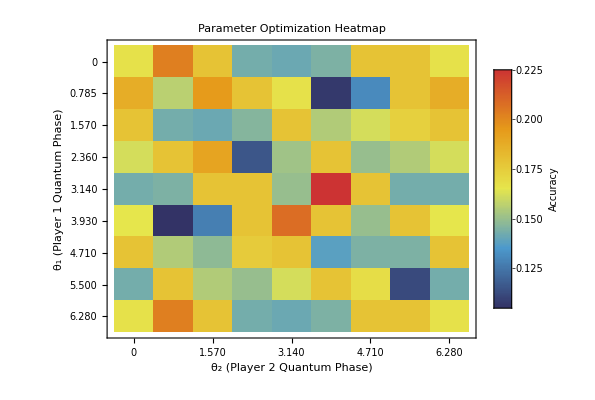

```mathematica
visualizeGridSearchResults[gridResults]
```

```mathematica
gridResults["bestTheta1"]
```

(5 π)/4

```mathematica
gridResults["bestTheta2"]
```

π

```mathematica
l1=1;
l2=1;
theta1 = π/2; (*N[gridResults["bestTheta1"]];*)
theta2=0;(* N[gridResults["bestTheta2"]]; *)
```

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2]
```

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=0, λ1=1, λ2=1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

```mathematica
getFirstNEntries[results,3]
```

Returning first 3 entries out of 579 total entries with extracted components.

```mathematica
{<|"SQ"->0.0436,"ACQ1"->0.0189,"ACQ2"->0.032,"NEGO"->0.22190000000000001,"CAP1"->0.14550000000000002,"CAP2"->0.1082,"WAR1"->0.22690000000000002,"WAR2"->0.2029,"prediction"->"WAR1","groundtruth"->"SQ","Agent1"->"ESTONIA","Agent2"->"UNITED KINGDOM"|>,<|"SQ"->0.09050000000000001,"ACQ1"->0.006900000000000001,"ACQ2"->0.11030000000000001,"NEGO"->0.2348,"CAP1"->0.0692,"CAP2"->0.1429,"WAR1"->0.1495,"WAR2"->0.19590000000000002,"prediction"->"NEGO","groundtruth"->"SQ","Agent1"->"FRANCE","Agent2"->"CHILE"|>,<|"SQ"->0.021500000000000002,"ACQ1"->0.019200000000000002,"ACQ2"->0.0417,"NEGO"->0.3252,"CAP1"->0.1378,"CAP2"->0.0664,"WAR1"->0.23670000000000002,"WAR2"->0.1515,"prediction"->"NEGO","groundtruth"->"SQ","Agent1"->"ARGENTINA","Agent2"->"FRANCE"|>}
```

{<|SQ→0.0436,ACQ1→0.0189,ACQ2→0.032,NEGO→0.2219,CAP1→0.1455,CAP2→0.1082,WAR1→0.2269,WAR2→0.2029,prediction→WAR1,groundtruth→SQ,Agent1→ESTONIA,Agent2→UNITED KINGDOM|>,<|SQ→0.0905,ACQ1→0.0069,ACQ2→0.1103,NEGO→0.2348,CAP1→0.0692,CAP2→0.1429,WAR1→0.1495,WAR2→0.1959,prediction→NEGO,groundtruth→SQ,Agent1→FRANCE,Agent2→CHILE|>,<|SQ→0.0215,ACQ1→0.0192,ACQ2→0.0417,NEGO→0.3252,CAP1→0.1378,CAP2→0.0664,WAR1→0.2367,WAR2→0.1515,prediction→NEGO,groundtruth→SQ,Agent1→ARGENTINA,Agent2→FRANCE|>}

```mathematica
exportPath=exportQuantumResultsToCSV[results,"D:\\home\\Documents\\Github\\quantum_international_interaction_game\\BN\\quantum_interaction_results_l1.csv"];
```

Processing 579 results for export...

Successfully exported 579 results to: D:\home\Documents\Github\quantum_international_interaction_game\BN\quantum_interaction_results_l1.csv

File contains 38 columns and 579 data rows

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

Final Accuracy: 0.17962

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```

Actual \ Predicted | ACQ1 | ACQ2 | CAP1 | CAP2 | NEGO | SQ | WAR1 | WAR2
ACQ1 | 0 | 5 | 0 | 0 | 0 | 0 | 1 | 0
ACQ2 | 0 | 78 | 0 | 0 | 0 | 0 | 21 | 0
CAP1 | 0 | 42 | 0 | 0 | 0 | 1 | 13 | 0
CAP2 | 3 | 69 | 0 | 0 | 0 | 1 | 26 | 0
NEGO | 0 | 71 | 0 | 0 | 0 | 2 | 26 | 0
SQ | 7 | 64 | 0 | 0 | 0 | 1 | 27 | 0
WAR1 | 0 | 74 | 0 | 0 | 0 | 0 | 25 | 0
WAR2 | 0 | 17 | 0 | 0 | 0 | 0 | 5 | 0

θ1 = Pi
--
2 θ2 = 0 λ1 = 1 λ2 = 1 | Accuracy = 0.17962

Quantum-Like Signorino Model Confusion Matrix

Quantum-Like Signorino Model Confusion Matrix

θ1 = 3.92699 θ2 = 3.14159 λ1 = 1 λ2 = 1 | Accuracy = 0.224525

Actual \ Predicted | ACQ1 | ACQ2 | CAP1 | CAP2 | NEGO | SQ | WAR1 | WAR2
ACQ1 | 0 | 1 | 0 | 0 | 4 | 0 | 1 | 0
ACQ2 | 0 | 43 | 0 | 0 | 19 | 0 | 36 | 1
CAP1 | 0 | 15 | 0 | 0 | 10 | 0 | 30 | 1
CAP2 | 0 | 39 | 0 | 0 | 17 | 0 | 42 | 1
NEGO | 0 | 15 | 0 | 0 | 28 | 0 | 53 | 3
SQ | 0 | 23 | 0 | 2 | 23 | 0 | 50 | 1
WAR1 | 0 | 21 | 0 | 0 | 16 | 0 | 59 | 3
WAR2 | 0 | 13 | 0 | 0 | 2 | 0 | 7 | 0

#### Setting 2: Lambda1 = 0.5 | Lambda2 = 0.5

```mathematica
datasetPath = "D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv"; 
data=loadData[datasetPath];
```

Loading CSV file: D:\home\Documents\Github\quantum_international_interaction_game\dataset\balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
gridsize = 9;
l1 =0.5;
l2=0.5;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

Starting grid search over 81 parameter combinations...

Theta1 range: {0,π/4,π/2,(3 π)/4,π,(5 π)/4,(3 π)/2,(7 π)/4,2 π}

Theta2 range: {0,π/4,π/2,(3 π)/4,π,(5 π)/4,(3 π)/2,(7 π)/4,2 π}

Lambda1 = 0.5, Lambda2 = 0.5

Dataset size: 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=0, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

New best found: θ1=0, θ2=0, Accuracy=0.174439

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=π/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=π/2, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 4/81 (4.94%)

Elapsed: 1.7 min, Estimated remaining: 32. min

Current best: θ1=0, θ2=0, Accuracy=0.174439

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(3 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(5 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(3 π)/2, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 8/81 (9.88%)

Elapsed: 4.1 min, Estimated remaining: 38. min

Current best: θ1=0, θ2=0, Accuracy=0.174439

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(7 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=2 π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=0, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

New best found: θ1=π/4, θ2=0, Accuracy=0.186528

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=π/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 12/81 (14.8%)

Elapsed: 6.6 min, Estimated remaining: 38. min

Current best: θ1=π/4, θ2=0, Accuracy=0.186528

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=π/2, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=(3 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=(5 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 16/81 (19.8%)

Elapsed: 9.2 min, Estimated remaining: 37. min

Current best: θ1=π/4, θ2=0, Accuracy=0.186528

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=(3 π)/2, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=(7 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=2 π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=0, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 20/81 (24.7%)

Elapsed: 12. min, Estimated remaining: 35. min

Current best: θ1=π/4, θ2=0, Accuracy=0.186528

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=π/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=π/2, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=(3 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 24/81 (29.6%)

Elapsed: 14. min, Estimated remaining: 33. min

Current best: θ1=π/4, θ2=0, Accuracy=0.186528

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=(5 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=(3 π)/2, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=(7 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=2 π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 28/81 (34.6%)

Elapsed: 16. min, Estimated remaining: 31. min

Current best: θ1=π/4, θ2=0, Accuracy=0.186528

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=0, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=π/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=π/2, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=(3 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 32/81 (39.5%)

Elapsed: 19. min, Estimated remaining: 29. min

Current best: θ1=π/4, θ2=0, Accuracy=0.186528

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=(5 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=(3 π)/2, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=(7 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 36/81 (44.4%)

Elapsed: 21. min, Estimated remaining: 27. min

Current best: θ1=π/4, θ2=0, Accuracy=0.186528

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=2 π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=0, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=π/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=π/2, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 40/81 (49.4%)

Elapsed: 24. min, Estimated remaining: 24. min

Current best: θ1=π/4, θ2=0, Accuracy=0.186528

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=(3 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=(5 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=(3 π)/2, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 44/81 (54.3%)

Elapsed: 26. min, Estimated remaining: 22. min

Current best: θ1=π/4, θ2=0, Accuracy=0.186528

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=(7 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=2 π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=0, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=π/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 48/81 (59.3%)

Elapsed: 28. min, Estimated remaining: 19. min

Current best: θ1=π/4, θ2=0, Accuracy=0.186528

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=π/2, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=(3 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=(5 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 52/81 (64.2%)

Elapsed: 31. min, Estimated remaining: 17. min

Current best: θ1=π/4, θ2=0, Accuracy=0.186528

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=(3 π)/2, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=(7 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=2 π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=0, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 56/81 (69.1%)

Elapsed: 33. min, Estimated remaining: 15. min

Current best: θ1=π/4, θ2=0, Accuracy=0.186528

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=π/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=π/2, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=(3 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 60/81 (74.1%)

Elapsed: 36. min, Estimated remaining: 13. min

Current best: θ1=π/4, θ2=0, Accuracy=0.186528

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=(5 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=(3 π)/2, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=(7 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=2 π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 64/81 (79.%)

Elapsed: 38. min, Estimated remaining: 10. min

Current best: θ1=π/4, θ2=0, Accuracy=0.186528

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=0, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=π/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=π/2, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=(3 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 68/81 (84.%)

Elapsed: 41. min, Estimated remaining: 7.8 min

Current best: θ1=π/4, θ2=0, Accuracy=0.186528

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=(5 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=(3 π)/2, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=(7 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 72/81 (88.9%)

Elapsed: 43. min, Estimated remaining: 5.4 min

Current best: θ1=π/4, θ2=0, Accuracy=0.186528

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=2 π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=0, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=π/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=π/2, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 76/81 (93.8%)

Elapsed: 45. min, Estimated remaining: 3. min

Current best: θ1=π/4, θ2=0, Accuracy=0.186528

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(3 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(5 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(3 π)/2, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 80/81 (98.8%)

Elapsed: 48. min, Estimated remaining: 0.6 min

Current best: θ1=π/4, θ2=0, Accuracy=0.186528

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(7 π)/4, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=2 π, λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Grid search completed!

Total time: 49. minutes

Best parameters found:

θ1 = π/4

θ2 = 0

Accuracy = 0.186528

Best parameters: θ1=π/4, θ2=0

Best accuracy: 0.186528

```mathematica
analyzeCurrentResults[gridResults]
```

analyzeCurrentResults[<|bestTheta1→π/4,bestTheta2→0,bestAccuracy→0.186528,allResults→{<|theta1→0,theta2→0,accuracy→0.174439,l1→0.5,l2→0.5|>,<|theta1→0,theta2→π/4,accuracy→0.164076,l1→0.5,l2→0.5|>,<|theta1→0,theta2→π/2,accuracy→0.169257,l1→0.5,l2→0.5|>,<|theta1→0,theta2→(3 π)/4,accuracy→0.165803,l1→0.5,l2→0.5|>,<|theta1→0,theta2→π,accuracy→0.146805,l1→0.5,l2→0.5|>,<|theta1→0,theta2→(5 π)/4,accuracy→0.170984,l1→0.5,l2→0.5|>,<|theta1→0,theta2→(3 π)/2,accuracy→0.169257,l1→0.5,l2→0.5|>,<|theta1→0,theta2→(7 π)/4,accuracy→0.134715,l1→0.5,l2→0.5|>,<|theta1→0,theta2→2 π,accuracy→0.174439,l1→0.5,l2→0.5|>,<|theta1→π/4,theta2→0,accuracy→0.186528,l1→0.5,l2→0.5|>,<|theta1→π/4,theta2→π/4,accuracy→0.164076,l1→0.5,l2→0.5|>,<|theta1→π/4,theta2→π/2,accuracy→0.145078,l1→0.5,l2→0.5|>,<|theta1→π/4,theta2→(3 π)/4,accuracy→0.169257,l1→0.5,l2→0.5|>,<|theta1→π/4,theta2→π,accuracy→0.150259,l1→0.5,l2→0.5|>,<|theta1→π/4,theta2→(5 π)/4,accuracy→0.132988,l1→0.5,l2→0.5|>,<|theta1→π/4,theta2→(3 π)/2,accuracy→0.138169,l1→0.5,l2→0.5|>,<|theta1→π/4,theta2→(7 π)/4,accuracy→0.169257,l1→0.5,l2→0.5|>,<|theta1→π/4,theta2→2 π,accuracy→0.186528,l1→0.5,l2→0.5|>,<|theta1→π/2,theta2→0,accuracy→0.169257,l1→0.5,l2→0.5|>,<|theta1→π/2,theta2→π/4,accuracy→0.15544,l1→0.5,l2→0.5|>,<|theta1→π/2,theta2→π/2,accuracy→0.145078,l1→0.5,l2→0.5|>,<|theta1→π/2,theta2→(3 π)/4,accuracy→0.174439,l1→0.5,l2→0.5|>,<|theta1→π/2,theta2→π,accuracy→0.169257,l1→0.5,l2→0.5|>,<|theta1→π/2,theta2→(5 π)/4,accuracy→0.134715,l1→0.5,l2→0.5|>,<|theta1→π/2,theta2→(3 π)/2,accuracy→0.136442,l1→0.5,l2→0.5|>,<|theta1→π/2,theta2→(7 π)/4,accuracy→0.165803,l1→0.5,l2→0.5|>,<|theta1→π/2,theta2→2 π,accuracy→0.169257,l1→0.5,l2→0.5|>,<|theta1→(3 π)/4,theta2→0,accuracy→0.145078,l1→0.5,l2→0.5|>,<|theta1→(3 π)/4,theta2→π/4,accuracy→0.169257,l1→0.5,l2→0.5|>,<|theta1→(3 π)/4,theta2→π/2,accuracy→0.146805,l1→0.5,l2→0.5|>,<|theta1→(3 π)/4,theta2→(3 π)/4,accuracy→0.134715,l1→0.5,l2→0.5|>,<|theta1→(3 π)/4,theta2→π,accuracy→0.139896,l1→0.5,l2→0.5|>,<|theta1→(3 π)/4,theta2→(5 π)/4,accuracy→0.169257,l1→0.5,l2→0.5|>,<|theta1→(3 π)/4,theta2→(3 π)/2,accuracy→0.177893,l1→0.5,l2→0.5|>,<|theta1→(3 π)/4,theta2→(7 π)/4,accuracy→0.158895,l1→0.5,l2→0.5|>,<|theta1→(3 π)/4,theta2→2 π,accuracy→0.145078,l1→0.5,l2→0.5|>,<|theta1→π,theta2→0,accuracy→0.146805,l1→0.5,l2→0.5|>,<|theta1→π,theta2→π/4,accuracy→0.169257,l1→0.5,l2→0.5|>,<|theta1→π,theta2→π/2,accuracy→0.169257,l1→0.5,l2→0.5|>,<|theta1→π,theta2→(3 π)/4,accuracy→0.132988,l1→0.5,l2→0.5|>,<|theta1→π,theta2→π,accuracy→0.174439,l1→0.5,l2→0.5|>,<|theta1→π,theta2→(5 π)/4,accuracy→0.164076,l1→0.5,l2→0.5|>,<|theta1→π,theta2→(3 π)/2,accuracy→0.169257,l1→0.5,l2→0.5|>,<|theta1→π,theta2→(7 π)/4,accuracy→0.169257,l1→0.5,l2→0.5|>,<|theta1→π,theta2→2 π,accuracy→0.146805,l1→0.5,l2→0.5|>,<|theta1→(5 π)/4,theta2→0,accuracy→0.148532,l1→0.5,l2→0.5|>,<|theta1→(5 π)/4,theta2→π/4,accuracy→0.132988,l1→0.5,l2→0.5|>,<|theta1→(5 π)/4,theta2→π/2,accuracy→0.139896,l1→0.5,l2→0.5|>,<|theta1→(5 π)/4,theta2→(3 π)/4,accuracy→0.169257,l1→0.5,l2→0.5|>,<|theta1→(5 π)/4,theta2→π,accuracy→0.181347,l1→0.5,l2→0.5|>,<|theta1→(5 π)/4,theta2→(5 π)/4,accuracy→0.181347,l1→0.5,l2→0.5|>,<|theta1→(5 π)/4,theta2→(3 π)/2,accuracy→0.146805,l1→0.5,l2→0.5|>,<|theta1→(5 π)/4,theta2→(7 π)/4,accuracy→0.169257,l1→0.5,l2→0.5|>,<|theta1→(5 π)/4,theta2→2 π,accuracy→0.148532,l1→0.5,l2→0.5|>,<|theta1→(3 π)/2,theta2→0,accuracy→0.169257,l1→0.5,l2→0.5|>,<|theta1→(3 π)/2,theta2→π/4,accuracy→0.132988,l1→0.5,l2→0.5|>,<|theta1→(3 π)/2,theta2→π/2,accuracy→0.165803,l1→0.5,l2→0.5|>,<|theta1→(3 π)/2,theta2→(3 π)/4,accuracy→0.170984,l1→0.5,l2→0.5|>,<|theta1→(3 π)/2,theta2→π,accuracy→0.169257,l1→0.5,l2→0.5|>,<|theta1→(3 π)/2,theta2→(5 π)/4,accuracy→0.165803,l1→0.5,l2→0.5|>,<|theta1→(3 π)/2,theta2→(3 π)/2,accuracy→0.146805,l1→0.5,l2→0.5|>,<|theta1→(3 π)/2,theta2→(7 π)/4,accuracy→0.170984,l1→0.5,l2→0.5|>,<|theta1→(3 π)/2,theta2→2 π,accuracy→0.169257,l1→0.5,l2→0.5|>,<|theta1→(7 π)/4,theta2→0,accuracy→0.138169,l1→0.5,l2→0.5|>,<|theta1→(7 π)/4,theta2→π/4,accuracy→0.169257,l1→0.5,l2→0.5|>,<|theta1→(7 π)/4,theta2→π/2,accuracy→0.176166,l1→0.5,l2→0.5|>,<|theta1→(7 π)/4,theta2→(3 π)/4,accuracy→0.160622,l1→0.5,l2→0.5|>,<|theta1→(7 π)/4,theta2→π,accuracy→0.145078,l1→0.5,l2→0.5|>,<|theta1→(7 π)/4,theta2→(5 π)/4,accuracy→0.169257,l1→0.5,l2→0.5|>,<|theta1→(7 π)/4,theta2→(3 π)/2,accuracy→0.150259,l1→0.5,l2→0.5|>,<|theta1→(7 π)/4,theta2→(7 π)/4,accuracy→0.122625,l1→0.5,l2→0.5|>,<|theta1→(7 π)/4,theta2→2 π,accuracy→0.138169,l1→0.5,l2→0.5|>,<|theta1→2 π,theta2→0,accuracy→0.174439,l1→0.5,l2→0.5|>,<|theta1→2 π,theta2→π/4,accuracy→0.164076,l1→0.5,l2→0.5|>,<|theta1→2 π,theta2→π/2,accuracy→0.169257,l1→0.5,l2→0.5|>,<|theta1→2 π,theta2→(3 π)/4,accuracy→0.165803,l1→0.5,l2→0.5|>,<|theta1→2 π,theta2→π,accuracy→0.146805,l1→0.5,l2→0.5|>,<|theta1→2 π,theta2→(5 π)/4,accuracy→0.170984,l1→0.5,l2→0.5|>,<|theta1→2 π,theta2→(3 π)/2,accuracy→0.169257,l1→0.5,l2→0.5|>,<|theta1→2 π,theta2→(7 π)/4,accuracy→0.134715,l1→0.5,l2→0.5|>,<|theta1→2 π,theta2→2 π,accuracy→0.174439,l1→0.5,l2→0.5|>},totalCombinations→81,l1→0.5,l2→0.5|>]

Grid Search Results Visualization

Parameter Space: 9 × 9 = 81 combinations

Best Parameters: θ₁ = 0.7854, θ₂ = 0 → Accuracy = 0.1865 (18.65%)

Accuracy Range: 0.123 - 0.187

Summary Statistics:

• Mean Accuracy: 0.159

• Standard Deviation: 0.015

• Improvement over Random: 4.37% points

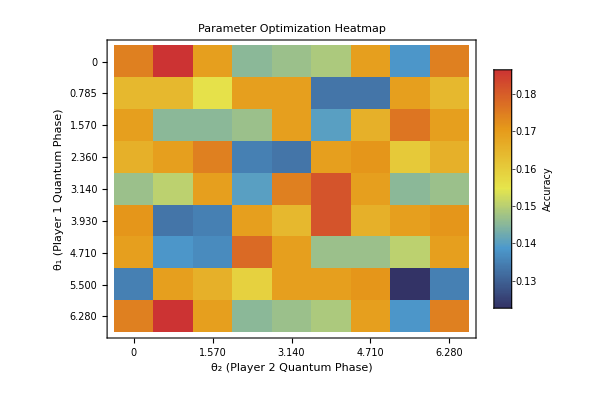

```mathematica
visualizeGridSearchResults[gridResults]
```

```mathematica
theta1 =N[gridResults["bestTheta1"]];
theta2=N[gridResults["bestTheta2"]];
```

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2];
```

Processing 579 rows with quantum model...

Parameters: θ1=0.785398, θ2=0., λ1=0.5, λ2=0.5

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

```mathematica
getFirstNEntries[results,3]
```

Returning first 3 entries out of 579 total entries with extracted components.

{<|SQ→0.0538,ACQ1→0.0217,ACQ2→0.1039,NEGO→0.1758,CAP1→0.1315,CAP2→0.1447,WAR1→0.213,WAR2→0.1556,prediction→WAR1,groundtruth→SQ,Agent1→ESTONIA,Agent2→UNITED KINGDOM|>,<|SQ→0.0318,ACQ1→0.0153,ACQ2→0.2082,NEGO→0.1674,CAP1→0.094,CAP2→0.1589,WAR1→0.1627,WAR2→0.1617,prediction→ACQ2,groundtruth→SQ,Agent1→FRANCE,Agent2→CHILE|>,<|SQ→0.0307,ACQ1→0.0388,ACQ2→0.0621,NEGO→0.2038,CAP1→0.1529,CAP2→0.1182,WAR1→0.2328,WAR2→0.1607,prediction→WAR1,groundtruth→SQ,Agent1→ARGENTINA,Agent2→FRANCE|>}

```mathematica
exportPath=exportQuantumResultsToCSV[results,"D:\\home\\Documents\\Github\\quantum_international_interaction_game\\BN\\quantum_interaction_results_l0.5.csv"];
```

Processing 579 results for export...

Successfully exported 579 results to: D:\home\Documents\Github\quantum_international_interaction_game\BN\quantum_interaction_results_l0.5.csv

File contains 38 columns and 579 data rows

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

Final Accuracy: 0.186528

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```

Quantum-Like Signorino Model Confusion Matrix

θ1 = 0.785398 θ2 = 0. λ1 = 0.5 λ2 = 0.5 | Accuracy = 0.186528

Actual \ Predicted | ACQ1 | ACQ2 | CAP1 | CAP2 | NEGO | SQ | WAR1 | WAR2
ACQ1 | 0 | 1 | 0 | 0 | 3 | 0 | 2 | 0
ACQ2 | 0 | 16 | 0 | 0 | 15 | 0 | 68 | 0
CAP1 | 0 | 9 | 0 | 0 | 9 | 0 | 38 | 0
CAP2 | 0 | 25 | 0 | 0 | 12 | 0 | 62 | 0
NEGO | 0 | 7 | 0 | 0 | 26 | 0 | 66 | 0
SQ | 0 | 13 | 0 | 2 | 13 | 0 | 70 | 1
WAR1 | 0 | 13 | 0 | 0 | 19 | 0 | 66 | 1
WAR2 | 0 | 8 | 0 | 0 | 1 | 0 | 13 | 0

#### Setting 3: Lambda1 = 2 | Lambda2 = 2

```mathematica
datasetPath = "D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";
(*"D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";*)
data=loadData[datasetPath];
```

Loading CSV file: D:\home\Documents\Github\quantum_international_interaction_game\dataset\balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
gridsize = 9;
l1 =2;
l2=2;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

Starting grid search over 81 parameter combinations...

Theta1 range: {0,π/4,π/2,(3 π)/4,π,(5 π)/4,(3 π)/2,(7 π)/4,2 π}

Theta2 range: {0,π/4,π/2,(3 π)/4,π,(5 π)/4,(3 π)/2,(7 π)/4,2 π}

Lambda1 = 2, Lambda2 = 2

Dataset size: 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=0, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

New best found: θ1=0, θ2=0, Accuracy=0.153713

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=π/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

New best found: θ1=0, θ2=π/4, Accuracy=0.186528

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=π/2, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 4/81 (4.94%)

Elapsed: 1.7 min, Estimated remaining: 32. min

Current best: θ1=0, θ2=π/4, Accuracy=0.186528

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(3 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(5 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(3 π)/2, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 8/81 (9.88%)

Elapsed: 4.1 min, Estimated remaining: 37. min

Current best: θ1=0, θ2=π/4, Accuracy=0.186528

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(7 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=2 π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=0, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

New best found: θ1=π/4, θ2=0, Accuracy=0.195164

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=π/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 12/81 (14.8%)

Elapsed: 6.5 min, Estimated remaining: 37. min

Current best: θ1=π/4, θ2=0, Accuracy=0.195164

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=π/2, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=(3 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=(5 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 16/81 (19.8%)

Elapsed: 9.3 min, Estimated remaining: 38. min

Current best: θ1=π/4, θ2=0, Accuracy=0.195164

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=(3 π)/2, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=(7 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=2 π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=0, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 20/81 (24.7%)

Elapsed: 12. min, Estimated remaining: 36. min

Current best: θ1=π/4, θ2=0, Accuracy=0.195164

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=π/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=π/2, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=(3 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 24/81 (29.6%)

Elapsed: 14. min, Estimated remaining: 34. min

Current best: θ1=π/4, θ2=0, Accuracy=0.195164

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=(5 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=(3 π)/2, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=(7 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=2 π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 28/81 (34.6%)

Elapsed: 17. min, Estimated remaining: 32. min

Current best: θ1=π/4, θ2=0, Accuracy=0.195164

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=0, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=π/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=π/2, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=(3 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 32/81 (39.5%)

Elapsed: 20. min, Estimated remaining: 30. min

Current best: θ1=π/4, θ2=0, Accuracy=0.195164

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=(5 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=(3 π)/2, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=(7 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 36/81 (44.4%)

Elapsed: 23. min, Estimated remaining: 29. min

Current best: θ1=π/4, θ2=0, Accuracy=0.195164

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=2 π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=0, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=π/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=π/2, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 40/81 (49.4%)

Elapsed: 27. min, Estimated remaining: 27. min

Current best: θ1=π/4, θ2=0, Accuracy=0.195164

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=(3 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=(5 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=(3 π)/2, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 44/81 (54.3%)

Elapsed: 29. min, Estimated remaining: 24. min

Current best: θ1=π/4, θ2=0, Accuracy=0.195164

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=(7 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=2 π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=0, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=π/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 48/81 (59.3%)

Elapsed: 32. min, Estimated remaining: 22. min

Current best: θ1=π/4, θ2=0, Accuracy=0.195164

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=π/2, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=(3 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

New best found: θ1=(5 π)/4, θ2=π, Accuracy=0.212435

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=(5 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 52/81 (64.2%)

Elapsed: 34. min, Estimated remaining: 19. min

Current best: θ1=(5 π)/4, θ2=π, Accuracy=0.212435

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=(3 π)/2, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=(7 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=2 π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=0, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 56/81 (69.1%)

Elapsed: 37. min, Estimated remaining: 16. min

Current best: θ1=(5 π)/4, θ2=π, Accuracy=0.212435

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=π/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=π/2, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=(3 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 60/81 (74.1%)

Elapsed: 39. min, Estimated remaining: 14. min

Current best: θ1=(5 π)/4, θ2=π, Accuracy=0.212435

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=(5 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=(3 π)/2, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=(7 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=2 π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 64/81 (79.%)

Elapsed: 42. min, Estimated remaining: 11. min

Current best: θ1=(5 π)/4, θ2=π, Accuracy=0.212435

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=0, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=π/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=π/2, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

New best found: θ1=(7 π)/4, θ2=π/2, Accuracy=0.219344

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=(3 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 68/81 (84.%)

Elapsed: 45. min, Estimated remaining: 8.6 min

Current best: θ1=(7 π)/4, θ2=π/2, Accuracy=0.219344

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=(5 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=(3 π)/2, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=(7 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 72/81 (88.9%)

Elapsed: 47. min, Estimated remaining: 5.9 min

Current best: θ1=(7 π)/4, θ2=π/2, Accuracy=0.219344

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=2 π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=0, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=π/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=π/2, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 76/81 (93.8%)

Elapsed: 50. min, Estimated remaining: 3.3 min

Current best: θ1=(7 π)/4, θ2=π/2, Accuracy=0.219344

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(3 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(5 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(3 π)/2, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 80/81 (98.8%)

Elapsed: 52. min, Estimated remaining: 0.66 min

Current best: θ1=(7 π)/4, θ2=π/2, Accuracy=0.219344

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(7 π)/4, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=2 π, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Grid search completed!

Total time: 54. minutes

Best parameters found:

θ1 = (7 π)/4

θ2 = π/2

Accuracy = 0.219344

Best parameters: θ1=(7 π)/4, θ2=π/2

Best accuracy: 0.219344

```mathematica
analyzeCurrentResults[gridResults]
```

analyzeCurrentResults[<|bestTheta1→(7 π)/4,bestTheta2→π/2,bestAccuracy→0.219344,allResults→{<|theta1→0,theta2→0,accuracy→0.153713,l1→2,l2→2|>,<|theta1→0,theta2→π/4,accuracy→0.186528,l1→2,l2→2|>,<|theta1→0,theta2→π/2,accuracy→0.183074,l1→2,l2→2|>,<|theta1→0,theta2→(3 π)/4,accuracy→0.148532,l1→2,l2→2|>,<|theta1→0,theta2→π,accuracy→0.158895,l1→2,l2→2|>,<|theta1→0,theta2→(5 π)/4,accuracy→0.151986,l1→2,l2→2|>,<|theta1→0,theta2→(3 π)/2,accuracy→0.183074,l1→2,l2→2|>,<|theta1→0,theta2→(7 π)/4,accuracy→0.16753,l1→2,l2→2|>,<|theta1→0,theta2→2 π,accuracy→0.153713,l1→2,l2→2|>,<|theta1→π/4,theta2→0,accuracy→0.195164,l1→2,l2→2|>,<|theta1→π/4,theta2→π/4,accuracy→0.170984,l1→2,l2→2|>,<|theta1→π/4,theta2→π/2,accuracy→0.129534,l1→2,l2→2|>,<|theta1→π/4,theta2→(3 π)/4,accuracy→0.183074,l1→2,l2→2|>,<|theta1→π/4,theta2→π,accuracy→0.143351,l1→2,l2→2|>,<|theta1→π/4,theta2→(5 π)/4,accuracy→0.115717,l1→2,l2→2|>,<|theta1→π/4,theta2→(3 π)/2,accuracy→0.172712,l1→2,l2→2|>,<|theta1→π/4,theta2→(7 π)/4,accuracy→0.183074,l1→2,l2→2|>,<|theta1→π/4,theta2→2 π,accuracy→0.195164,l1→2,l2→2|>,<|theta1→π/2,theta2→0,accuracy→0.183074,l1→2,l2→2|>,<|theta1→π/2,theta2→π/4,accuracy→0.186528,l1→2,l2→2|>,<|theta1→π/2,theta2→π/2,accuracy→0.157168,l1→2,l2→2|>,<|theta1→π/2,theta2→(3 π)/4,accuracy→0.17962,l1→2,l2→2|>,<|theta1→π/2,theta2→π,accuracy→0.183074,l1→2,l2→2|>,<|theta1→π/2,theta2→(5 π)/4,accuracy→0.184801,l1→2,l2→2|>,<|theta1→π/2,theta2→(3 π)/2,accuracy→0.145078,l1→2,l2→2|>,<|theta1→π/2,theta2→(7 π)/4,accuracy→0.188256,l1→2,l2→2|>,<|theta1→π/2,theta2→2 π,accuracy→0.183074,l1→2,l2→2|>,<|theta1→(3 π)/4,theta2→0,accuracy→0.138169,l1→2,l2→2|>,<|theta1→(3 π)/4,theta2→π/4,accuracy→0.183074,l1→2,l2→2|>,<|theta1→(3 π)/4,theta2→π/2,accuracy→0.15544,l1→2,l2→2|>,<|theta1→(3 π)/4,theta2→(3 π)/4,accuracy→0.129534,l1→2,l2→2|>,<|theta1→(3 π)/4,theta2→π,accuracy→0.176166,l1→2,l2→2|>,<|theta1→(3 π)/4,theta2→(5 π)/4,accuracy→0.183074,l1→2,l2→2|>,<|theta1→(3 π)/4,theta2→(3 π)/2,accuracy→0.189983,l1→2,l2→2|>,<|theta1→(3 π)/4,theta2→(7 π)/4,accuracy→0.169257,l1→2,l2→2|>,<|theta1→(3 π)/4,theta2→2 π,accuracy→0.138169,l1→2,l2→2|>,<|theta1→π,theta2→0,accuracy→0.158895,l1→2,l2→2|>,<|theta1→π,theta2→π/4,accuracy→0.151986,l1→2,l2→2|>,<|theta1→π,theta2→π/2,accuracy→0.183074,l1→2,l2→2|>,<|theta1→π,theta2→(3 π)/4,accuracy→0.170984,l1→2,l2→2|>,<|theta1→π,theta2→π,accuracy→0.139896,l1→2,l2→2|>,<|theta1→π,theta2→(5 π)/4,accuracy→0.170984,l1→2,l2→2|>,<|theta1→π,theta2→(3 π)/2,accuracy→0.183074,l1→2,l2→2|>,<|theta1→π,theta2→(7 π)/4,accuracy→0.145078,l1→2,l2→2|>,<|theta1→π,theta2→2 π,accuracy→0.158895,l1→2,l2→2|>,<|theta1→(5 π)/4,theta2→0,accuracy→0.146805,l1→2,l2→2|>,<|theta1→(5 π)/4,theta2→π/4,accuracy→0.126079,l1→2,l2→2|>,<|theta1→(5 π)/4,theta2→π/2,accuracy→0.17962,l1→2,l2→2|>,<|theta1→(5 π)/4,theta2→(3 π)/4,accuracy→0.183074,l1→2,l2→2|>,<|theta1→(5 π)/4,theta2→π,accuracy→0.212435,l1→2,l2→2|>,<|theta1→(5 π)/4,theta2→(5 π)/4,accuracy→0.169257,l1→2,l2→2|>,<|theta1→(5 π)/4,theta2→(3 π)/2,accuracy→0.131261,l1→2,l2→2|>,<|theta1→(5 π)/4,theta2→(7 π)/4,accuracy→0.183074,l1→2,l2→2|>,<|theta1→(5 π)/4,theta2→2 π,accuracy→0.146805,l1→2,l2→2|>,<|theta1→(3 π)/2,theta2→0,accuracy→0.183074,l1→2,l2→2|>,<|theta1→(3 π)/2,theta2→π/4,accuracy→0.146805,l1→2,l2→2|>,<|theta1→(3 π)/2,theta2→π/2,accuracy→0.169257,l1→2,l2→2|>,<|theta1→(3 π)/2,theta2→(3 π)/4,accuracy→0.153713,l1→2,l2→2|>,<|theta1→(3 π)/2,theta2→π,accuracy→0.183074,l1→2,l2→2|>,<|theta1→(3 π)/2,theta2→(5 π)/4,accuracy→0.146805,l1→2,l2→2|>,<|theta1→(3 π)/2,theta2→(3 π)/2,accuracy→0.160622,l1→2,l2→2|>,<|theta1→(3 π)/2,theta2→(7 π)/4,accuracy→0.151986,l1→2,l2→2|>,<|theta1→(3 π)/2,theta2→2 π,accuracy→0.183074,l1→2,l2→2|>,<|theta1→(7 π)/4,theta2→0,accuracy→0.183074,l1→2,l2→2|>,<|theta1→(7 π)/4,theta2→π/4,accuracy→0.183074,l1→2,l2→2|>,<|theta1→(7 π)/4,theta2→π/2,accuracy→0.219344,l1→2,l2→2|>,<|theta1→(7 π)/4,theta2→(3 π)/4,accuracy→0.16753,l1→2,l2→2|>,<|theta1→(7 π)/4,theta2→π,accuracy→0.138169,l1→2,l2→2|>,<|theta1→(7 π)/4,theta2→(5 π)/4,accuracy→0.183074,l1→2,l2→2|>,<|theta1→(7 π)/4,theta2→(3 π)/2,accuracy→0.145078,l1→2,l2→2|>,<|theta1→(7 π)/4,theta2→(7 π)/4,accuracy→0.136442,l1→2,l2→2|>,<|theta1→(7 π)/4,theta2→2 π,accuracy→0.183074,l1→2,l2→2|>,<|theta1→2 π,theta2→0,accuracy→0.153713,l1→2,l2→2|>,<|theta1→2 π,theta2→π/4,accuracy→0.186528,l1→2,l2→2|>,<|theta1→2 π,theta2→π/2,accuracy→0.183074,l1→2,l2→2|>,<|theta1→2 π,theta2→(3 π)/4,accuracy→0.148532,l1→2,l2→2|>,<|theta1→2 π,theta2→π,accuracy→0.158895,l1→2,l2→2|>,<|theta1→2 π,theta2→(5 π)/4,accuracy→0.151986,l1→2,l2→2|>,<|theta1→2 π,theta2→(3 π)/2,accuracy→0.183074,l1→2,l2→2|>,<|theta1→2 π,theta2→(7 π)/4,accuracy→0.16753,l1→2,l2→2|>,<|theta1→2 π,theta2→2 π,accuracy→0.153713,l1→2,l2→2|>},totalCombinations→81,l1→2,l2→2|>]

Grid Search Results Visualization

Parameter Space: 9 × 9 = 81 combinations

Best Parameters: θ₁ = 5.4980, θ₂ = 1.5710 → Accuracy = 0.2193 (21.93%)

Accuracy Range: 0.116 - 0.219

Summary Statistics:

• Mean Accuracy: 0.166

• Standard Deviation: 0.021

• Improvement over Random: 7.65% points

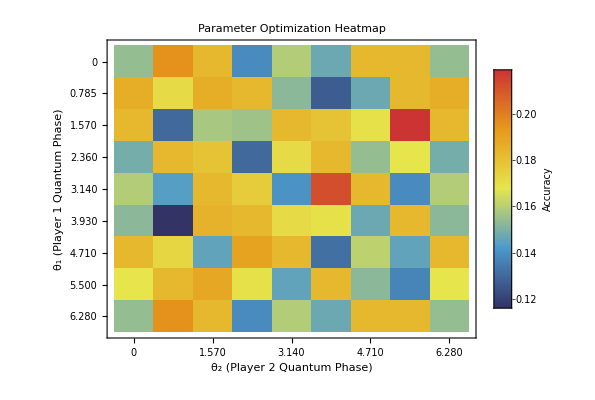

```mathematica
visualizeGridSearchResults[gridResults]
```

```mathematica
theta1 =N[gridResults["bestTheta1"]];
theta2=N[gridResults["bestTheta2"]];
```

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2];
```

Processing 579 rows with quantum model...

Parameters: θ1=5.49779, θ2=1.5708, λ1=2, λ2=2

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

```mathematica
getFirstNEntries[results,3]
```

Returning first 3 entries out of 579 total entries with extracted components.

{<|SQ→-0.0036,ACQ1→-0.1111,ACQ2→-0.055,NEGO→0.3176,CAP1→0.1863,CAP2→0.1047,WAR1→0.2841,WAR2→0.2769,prediction→NEGO,groundtruth→SQ,Agent1→ESTONIA,Agent2→UNITED KINGDOM|>,<|SQ→0.2472,ACQ1→0.0002,ACQ2→1.9465,NEGO→-0.3298,CAP1→-0.0485,CAP2→-0.2463,WAR1→-0.2655,WAR2→-0.3038,prediction→ACQ2,groundtruth→SQ,Agent1→FRANCE,Agent2→CHILE|>,<|SQ→1.2954,ACQ1→6.1874,ACQ2→0.0002,NEGO→-1.7095,CAP1→-1.565,CAP2→-0.1435,WAR1→-1.2651,WAR2→-1.7999,prediction→ACQ1,groundtruth→SQ,Agent1→ARGENTINA,Agent2→FRANCE|>}

```mathematica
exportPath=exportQuantumResultsToCSV[results,"D:\\home\\Documents\\Github\\quantum_international_interaction_game\\BN\\quantum_interaction_results_l2.csv"];
```

Processing 579 results for export...

Successfully exported 579 results to: D:\home\Documents\Github\quantum_international_interaction_game\BN\quantum_interaction_results_l2.csv

File contains 38 columns and 579 data rows

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

Final Accuracy: 0.219344

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```

Quantum-Like Signorino Model Confusion Matrix

θ1 = 5.49779 θ2 = 1.5708 λ1 = 2 λ2 = 2 | Accuracy = 0.219344

Actual \ Predicted | ACQ1 | ACQ2 | CAP1 | CAP2 | NEGO | SQ | WAR1 | WAR2
ACQ1 | 0 | 2 | 0 | 0 | 2 | 0 | 1 | 1
ACQ2 | 2 | 41 | 1 | 0 | 27 | 0 | 23 | 5
CAP1 | 0 | 16 | 0 | 0 | 15 | 1 | 20 | 4
CAP2 | 1 | 40 | 0 | 0 | 27 | 1 | 25 | 5
NEGO | 1 | 16 | 4 | 0 | 45 | 0 | 25 | 8
SQ | 4 | 21 | 1 | 2 | 39 | 2 | 27 | 3
WAR1 | 1 | 24 | 2 | 0 | 26 | 0 | 37 | 9
WAR2 | 0 | 11 | 0 | 0 | 5 | 0 | 4 | 2

#### Setting 4: Lambda1 = 0.1 | Lambda2 = 0.1

```mathematica
datasetPath = "D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv" ;
(*"D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";*)
data=loadData[datasetPath];
```

Loading CSV file: D:\home\Documents\Github\quantum_international_interaction_game\dataset\balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
gridsize = 9;
l1 =0.1;
l2=0.1;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

Starting grid search over 81 parameter combinations...

Theta1 range: {0,π/4,π/2,(3 π)/4,π,(5 π)/4,(3 π)/2,(7 π)/4,2 π}

Theta2 range: {0,π/4,π/2,(3 π)/4,π,(5 π)/4,(3 π)/2,(7 π)/4,2 π}

Lambda1 = 0.1, Lambda2 = 0.1

Dataset size: 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=0, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

New best found: θ1=0, θ2=0, Accuracy=0.165803

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=π/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

New best found: θ1=0, θ2=π/4, Accuracy=0.176166

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=π/2, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 4/81 (4.94%)

Elapsed: 1.7 min, Estimated remaining: 33. min

Current best: θ1=0, θ2=π/4, Accuracy=0.176166

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(3 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(5 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(3 π)/2, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 8/81 (9.88%)

Elapsed: 4.2 min, Estimated remaining: 38. min

Current best: θ1=0, θ2=π/4, Accuracy=0.176166

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(7 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=2 π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=0, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

New best found: θ1=π/4, θ2=0, Accuracy=0.177893

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=π/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 12/81 (14.8%)

Elapsed: 6.6 min, Estimated remaining: 38. min

Current best: θ1=π/4, θ2=0, Accuracy=0.177893

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=π/2, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=(3 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=(5 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 16/81 (19.8%)

Elapsed: 9.3 min, Estimated remaining: 38. min

Current best: θ1=π/4, θ2=0, Accuracy=0.177893

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=(3 π)/2, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=(7 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=2 π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=0, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 20/81 (24.7%)

Elapsed: 12. min, Estimated remaining: 36. min

Current best: θ1=π/4, θ2=0, Accuracy=0.177893

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=π/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=π/2, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=(3 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 24/81 (29.6%)

Elapsed: 14. min, Estimated remaining: 34. min

Current best: θ1=π/4, θ2=0, Accuracy=0.177893

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=(5 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=(3 π)/2, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=(7 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=2 π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 28/81 (34.6%)

Elapsed: 17. min, Estimated remaining: 32. min

Current best: θ1=π/4, θ2=0, Accuracy=0.177893

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=0, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=π/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=π/2, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=(3 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 32/81 (39.5%)

Elapsed: 20. min, Estimated remaining: 30. min

Current best: θ1=π/4, θ2=0, Accuracy=0.177893

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=(5 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=(3 π)/2, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=(7 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 36/81 (44.4%)

Elapsed: 22. min, Estimated remaining: 28. min

Current best: θ1=π/4, θ2=0, Accuracy=0.177893

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=2 π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=0, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=π/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=π/2, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 40/81 (49.4%)

Elapsed: 25. min, Estimated remaining: 26. min

Current best: θ1=π/4, θ2=0, Accuracy=0.177893

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=(3 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=(5 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=(3 π)/2, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 44/81 (54.3%)

Elapsed: 27. min, Estimated remaining: 23. min

Current best: θ1=π/4, θ2=0, Accuracy=0.177893

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=(7 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π, θ2=2 π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=0, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=π/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 48/81 (59.3%)

Elapsed: 30. min, Estimated remaining: 21. min

Current best: θ1=π/4, θ2=0, Accuracy=0.177893

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=π/2, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=(3 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=(5 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 52/81 (64.2%)

Elapsed: 33. min, Estimated remaining: 19. min

Current best: θ1=π/4, θ2=0, Accuracy=0.177893

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=(3 π)/2, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=(7 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(5 π)/4, θ2=2 π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=0, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 56/81 (69.1%)

Elapsed: 36. min, Estimated remaining: 16. min

Current best: θ1=π/4, θ2=0, Accuracy=0.177893

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=π/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=π/2, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=(3 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 60/81 (74.1%)

Elapsed: 38. min, Estimated remaining: 13. min

Current best: θ1=π/4, θ2=0, Accuracy=0.177893

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=(5 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=(3 π)/2, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=(7 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/2, θ2=2 π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 64/81 (79.%)

Elapsed: 41. min, Estimated remaining: 11. min

Current best: θ1=π/4, θ2=0, Accuracy=0.177893

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=0, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=π/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=π/2, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=(3 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 68/81 (84.%)

Elapsed: 44. min, Estimated remaining: 8.3 min

Current best: θ1=π/4, θ2=0, Accuracy=0.177893

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=(5 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=(3 π)/2, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=(7 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 72/81 (88.9%)

Elapsed: 46. min, Estimated remaining: 5.8 min

Current best: θ1=π/4, θ2=0, Accuracy=0.177893

Processing 579 rows with quantum model...

Parameters: θ1=(7 π)/4, θ2=2 π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=0, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=π/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=π/2, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 76/81 (93.8%)

Elapsed: 49. min, Estimated remaining: 3.2 min

Current best: θ1=π/4, θ2=0, Accuracy=0.177893

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(3 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(5 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(3 π)/2, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 80/81 (98.8%)

Elapsed: 51. min, Estimated remaining: 0.64 min

Current best: θ1=π/4, θ2=0, Accuracy=0.177893

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=(7 π)/4, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=2 π, θ2=2 π, λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Grid search completed!

Total time: 52. minutes

Best parameters found:

θ1 = π/4

θ2 = 0

Accuracy = 0.177893

Best parameters: θ1=π/4, θ2=0

Best accuracy: 0.177893

```mathematica
analyzeCurrentResults[gridResults]
```

analyzeCurrentResults[<|bestTheta1→π/4,bestTheta2→0,bestAccuracy→0.177893,allResults→{<|theta1→0,theta2→0,accuracy→0.165803,l1→0.1,l2→0.1|>,<|theta1→0,theta2→π/4,accuracy→0.176166,l1→0.1,l2→0.1|>,<|theta1→0,theta2→π/2,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→0,theta2→(3 π)/4,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→0,theta2→π,accuracy→0.170984,l1→0.1,l2→0.1|>,<|theta1→0,theta2→(5 π)/4,accuracy→0.157168,l1→0.1,l2→0.1|>,<|theta1→0,theta2→(3 π)/2,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→0,theta2→(7 π)/4,accuracy→0.148532,l1→0.1,l2→0.1|>,<|theta1→0,theta2→2 π,accuracy→0.165803,l1→0.1,l2→0.1|>,<|theta1→π/4,theta2→0,accuracy→0.177893,l1→0.1,l2→0.1|>,<|theta1→π/4,theta2→π/4,accuracy→0.174439,l1→0.1,l2→0.1|>,<|theta1→π/4,theta2→π/2,accuracy→0.157168,l1→0.1,l2→0.1|>,<|theta1→π/4,theta2→(3 π)/4,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→π/4,theta2→π,accuracy→0.165803,l1→0.1,l2→0.1|>,<|theta1→π/4,theta2→(5 π)/4,accuracy→0.157168,l1→0.1,l2→0.1|>,<|theta1→π/4,theta2→(3 π)/2,accuracy→0.158895,l1→0.1,l2→0.1|>,<|theta1→π/4,theta2→(7 π)/4,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→π/4,theta2→2 π,accuracy→0.177893,l1→0.1,l2→0.1|>,<|theta1→π/2,theta2→0,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→π/2,theta2→π/4,accuracy→0.176166,l1→0.1,l2→0.1|>,<|theta1→π/2,theta2→π/2,accuracy→0.170984,l1→0.1,l2→0.1|>,<|theta1→π/2,theta2→(3 π)/4,accuracy→0.160622,l1→0.1,l2→0.1|>,<|theta1→π/2,theta2→π,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→π/2,theta2→(5 π)/4,accuracy→0.148532,l1→0.1,l2→0.1|>,<|theta1→π/2,theta2→(3 π)/2,accuracy→0.162349,l1→0.1,l2→0.1|>,<|theta1→π/2,theta2→(7 π)/4,accuracy→0.177893,l1→0.1,l2→0.1|>,<|theta1→π/2,theta2→2 π,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→(3 π)/4,theta2→0,accuracy→0.157168,l1→0.1,l2→0.1|>,<|theta1→(3 π)/4,theta2→π/4,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→(3 π)/4,theta2→π/2,accuracy→0.165803,l1→0.1,l2→0.1|>,<|theta1→(3 π)/4,theta2→(3 π)/4,accuracy→0.162349,l1→0.1,l2→0.1|>,<|theta1→(3 π)/4,theta2→π,accuracy→0.157168,l1→0.1,l2→0.1|>,<|theta1→(3 π)/4,theta2→(5 π)/4,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→(3 π)/4,theta2→(3 π)/2,accuracy→0.177893,l1→0.1,l2→0.1|>,<|theta1→(3 π)/4,theta2→(7 π)/4,accuracy→0.176166,l1→0.1,l2→0.1|>,<|theta1→(3 π)/4,theta2→2 π,accuracy→0.157168,l1→0.1,l2→0.1|>,<|theta1→π,theta2→0,accuracy→0.170984,l1→0.1,l2→0.1|>,<|theta1→π,theta2→π/4,accuracy→0.158895,l1→0.1,l2→0.1|>,<|theta1→π,theta2→π/2,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→π,theta2→(3 π)/4,accuracy→0.148532,l1→0.1,l2→0.1|>,<|theta1→π,theta2→π,accuracy→0.162349,l1→0.1,l2→0.1|>,<|theta1→π,theta2→(5 π)/4,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→π,theta2→(3 π)/2,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→π,theta2→(7 π)/4,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→π,theta2→2 π,accuracy→0.170984,l1→0.1,l2→0.1|>,<|theta1→(5 π)/4,theta2→0,accuracy→0.165803,l1→0.1,l2→0.1|>,<|theta1→(5 π)/4,theta2→π/4,accuracy→0.157168,l1→0.1,l2→0.1|>,<|theta1→(5 π)/4,theta2→π/2,accuracy→0.15544,l1→0.1,l2→0.1|>,<|theta1→(5 π)/4,theta2→(3 π)/4,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→(5 π)/4,theta2→π,accuracy→0.176166,l1→0.1,l2→0.1|>,<|theta1→(5 π)/4,theta2→(5 π)/4,accuracy→0.177893,l1→0.1,l2→0.1|>,<|theta1→(5 π)/4,theta2→(3 π)/2,accuracy→0.158895,l1→0.1,l2→0.1|>,<|theta1→(5 π)/4,theta2→(7 π)/4,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→(5 π)/4,theta2→2 π,accuracy→0.165803,l1→0.1,l2→0.1|>,<|theta1→(3 π)/2,theta2→0,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→(3 π)/2,theta2→π/4,accuracy→0.150259,l1→0.1,l2→0.1|>,<|theta1→(3 π)/2,theta2→π/2,accuracy→0.16753,l1→0.1,l2→0.1|>,<|theta1→(3 π)/2,theta2→(3 π)/4,accuracy→0.174439,l1→0.1,l2→0.1|>,<|theta1→(3 π)/2,theta2→π,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→(3 π)/2,theta2→(5 π)/4,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→(3 π)/2,theta2→(3 π)/2,accuracy→0.170984,l1→0.1,l2→0.1|>,<|theta1→(3 π)/2,theta2→(7 π)/4,accuracy→0.15544,l1→0.1,l2→0.1|>,<|theta1→(3 π)/2,theta2→2 π,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→(7 π)/4,theta2→0,accuracy→0.15544,l1→0.1,l2→0.1|>,<|theta1→(7 π)/4,theta2→π/4,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→(7 π)/4,theta2→π/2,accuracy→0.177893,l1→0.1,l2→0.1|>,<|theta1→(7 π)/4,theta2→(3 π)/4,accuracy→0.176166,l1→0.1,l2→0.1|>,<|theta1→(7 π)/4,theta2→π,accuracy→0.157168,l1→0.1,l2→0.1|>,<|theta1→(7 π)/4,theta2→(5 π)/4,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→(7 π)/4,theta2→(3 π)/2,accuracy→0.165803,l1→0.1,l2→0.1|>,<|theta1→(7 π)/4,theta2→(7 π)/4,accuracy→0.150259,l1→0.1,l2→0.1|>,<|theta1→(7 π)/4,theta2→2 π,accuracy→0.15544,l1→0.1,l2→0.1|>,<|theta1→2 π,theta2→0,accuracy→0.165803,l1→0.1,l2→0.1|>,<|theta1→2 π,theta2→π/4,accuracy→0.176166,l1→0.1,l2→0.1|>,<|theta1→2 π,theta2→π/2,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→2 π,theta2→(3 π)/4,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→2 π,theta2→π,accuracy→0.170984,l1→0.1,l2→0.1|>,<|theta1→2 π,theta2→(5 π)/4,accuracy→0.157168,l1→0.1,l2→0.1|>,<|theta1→2 π,theta2→(3 π)/2,accuracy→0.172712,l1→0.1,l2→0.1|>,<|theta1→2 π,theta2→(7 π)/4,accuracy→0.148532,l1→0.1,l2→0.1|>,<|theta1→2 π,theta2→2 π,accuracy→0.165803,l1→0.1,l2→0.1|>},totalCombinations→81,l1→0.1,l2→0.1|>]

Grid Search Results Visualization

Parameter Space: 9 × 9 = 81 combinations

Best Parameters: θ₁ = 0.7854, θ₂ = 0 → Accuracy = 0.1779 (17.79%)

Accuracy Range: 0.149 - 0.178

Summary Statistics:

• Mean Accuracy: 0.167

• Standard Deviation: 0.009

• Improvement over Random: 3.50% points

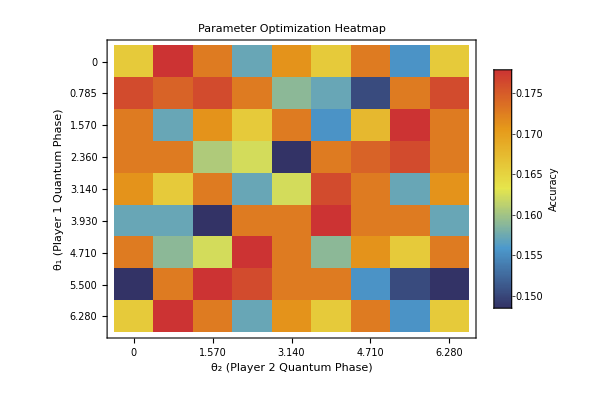

```mathematica
visualizeGridSearchResults[gridResults]
```

```mathematica
theta1 =N[gridResults["bestTheta1"]];
theta2=N[gridResults["bestTheta2"]];
```

```mathematica
Print[gridResults["bestTheta1"]];
Print[gridResults["bestTheta2"]];
```

π/4

0

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2];
```

Processing 579 rows with quantum model...

Parameters: θ1=0.785398, θ2=0., λ1=0.1, λ2=0.1

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

```mathematica
getFirstNEntries[results,3]
```

Returning first 3 entries out of 579 total entries with extracted components.

{<|SQ→0.0781,ACQ1→0.0369,ACQ2→0.0907,NEGO→0.1761,CAP1→0.1403,CAP2→0.1601,WAR1→0.1728,WAR2→0.1451,prediction→NEGO,groundtruth→SQ,Agent1→ESTONIA,Agent2→UNITED KINGDOM|>,<|SQ→0.0726,ACQ1→0.0375,ACQ2→0.1022,NEGO→0.1758,CAP1→0.1343,CAP2→0.1634,WAR1→0.1642,WAR2→0.15,prediction→NEGO,groundtruth→SQ,Agent1→FRANCE,Agent2→CHILE|>,<|SQ→0.0713,ACQ1→0.0411,ACQ2→0.0867,NEGO→0.1798,CAP1→0.142,CAP2→0.1568,WAR1→0.1791,WAR2→0.1434,prediction→NEGO,groundtruth→SQ,Agent1→ARGENTINA,Agent2→FRANCE|>}

```mathematica
exportPath=exportQuantumResultsToCSV[results,"D:\\home\\Documents\\Github\\quantum_international_interaction_game\\BN\\quantum_interaction_results_l0.1.csv"];
```

Processing 579 results for export...

Successfully exported 579 results to: D:\home\Documents\Github\quantum_international_interaction_game\BN\quantum_interaction_results_l0.1.csv

File contains 38 columns and 579 data rows

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

Final Accuracy: 0.177893

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```

Quantum-Like Signorino Model Confusion Matrix

θ1 = 0.785398 θ2 = 0. λ1 = 0.1 λ2 = 0.1 | Accuracy = 0.177893

Actual \ Predicted | ACQ1 | ACQ2 | CAP1 | CAP2 | NEGO | SQ | WAR1 | WAR2
ACQ1 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0
ACQ2 | 0 | 0 | 0 | 0 | 95 | 0 | 4 | 0
CAP1 | 0 | 0 | 0 | 0 | 50 | 0 | 6 | 0
CAP2 | 0 | 0 | 0 | 0 | 84 | 0 | 15 | 0
NEGO | 0 | 0 | 0 | 0 | 94 | 0 | 5 | 0
SQ | 0 | 0 | 0 | 0 | 92 | 0 | 7 | 0
WAR1 | 0 | 0 | 0 | 0 | 90 | 0 | 9 | 0
WAR2 | 0 | 0 | 0 | 0 | 22 | 0 | 0 | 0

#### Setting 5: Lambda1 = 10 | Lambda2 = 10

```mathematica
datasetPath ="D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv" ;
(*"D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";*)
data=loadData[datasetPath];
```

Loading CSV file: D:\home\Documents\Github\quantum_international_interaction_game\dataset\balanced_data.csv

Loaded 579 rows with 149 columns

```mathematica
gridsize = 9;
l1 =10;
l2=10;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

Starting grid search over 81 parameter combinations...

Theta1 range: {0,π/4,π/2,(3 π)/4,π,(5 π)/4,(3 π)/2,(7 π)/4,2 π}

Theta2 range: {0,π/4,π/2,(3 π)/4,π,(5 π)/4,(3 π)/2,(7 π)/4,2 π}

Lambda1 = 10, Lambda2 = 10

Dataset size: 579 rows

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=0, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

New best found: θ1=0, θ2=0, Accuracy=0.150259

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=π/4, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

New best found: θ1=0, θ2=π/4, Accuracy=0.172712

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=π/2, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 4/81 (4.94%)

Elapsed: 1.6 min, Estimated remaining: 30. min

Current best: θ1=0, θ2=π/4, Accuracy=0.172712

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(3 π)/4, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=π, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(5 π)/4, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(3 π)/2, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 8/81 (9.88%)

Elapsed: 3.9 min, Estimated remaining: 35. min

Current best: θ1=0, θ2=π/4, Accuracy=0.172712

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=(7 π)/4, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=0, θ2=2 π, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=0, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=π/4, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 12/81 (14.8%)

Elapsed: 6.1 min, Estimated remaining: 35. min

Current best: θ1=0, θ2=π/4, Accuracy=0.172712

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=π/2, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=(3 π)/4, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=π, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=(5 π)/4, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 16/81 (19.8%)

Elapsed: 8.6 min, Estimated remaining: 35. min

Current best: θ1=0, θ2=π/4, Accuracy=0.172712

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=(3 π)/2, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=(7 π)/4, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/4, θ2=2 π, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=0, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 20/81 (24.7%)

Elapsed: 12. min, Estimated remaining: 37. min

Current best: θ1=0, θ2=π/4, Accuracy=0.172712

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=π/4, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=π/2, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=(3 π)/4, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

New best found: θ1=π/2, θ2=(3 π)/4, Accuracy=0.176166

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=π, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 24/81 (29.6%)

Elapsed: 15. min, Estimated remaining: 35. min

Current best: θ1=π/2, θ2=(3 π)/4, Accuracy=0.176166

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=(5 π)/4, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=(3 π)/2, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=(7 π)/4, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=π/2, θ2=2 π, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Progress: 28/81 (34.6%)

Elapsed: 19. min, Estimated remaining: 37. min

Current best: θ1=π/2, θ2=(3 π)/4, Accuracy=0.176166

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=0, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=π/4, λ1=10, λ2=10

Processing row 50/579

Processing row 100/579

Processing row 150/579

Processing row 200/579

Processing row 250/579

Processing row 300/579

Processing row 350/579

Processing row 400/579

Processing row 450/579

Processing row 500/579

Processing row 550/579

Successfully processed 579 out of 579 rows

579

Processing 579 rows with quantum model...

Parameters: θ1=(3 π)/4, θ2=π/2, λ1=10, λ2=10

Processing row 50/579

$Aborted

Best parameters: θ1=π/4, θ2=0

Best accuracy: 0.177893

```mathematica
analyzeCurrentResults[gridResults]
```

```mathematica
visualizeGridSearchResults[gridResults]
```

```mathematica
theta1 =N[gridResults["bestTheta1"]];
theta2=N[gridResults["bestTheta2"]];
```

```mathematica
Print[gridResults["bestTheta1"]];
Print[gridResults["bestTheta2"]];
```

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2];
```

```mathematica
getFirstNEntries[results,3]
```

```mathematica
exportPath=exportQuantumResultsToCSV[results,"D:\\home\\Documents\\Github\\quantum_international_interaction_game\\BN\\quantum_interaction_results_l10.csv"];
```

```mathematica
accuracy=calculateQuantumAccuracy[results];
Print["Final Accuracy: ",N[accuracy]];
```

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```

#### Setting 6: Lambda1 = 0.0001 | Lambda2 = 0.0001

```mathematica
datasetPath ="D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv" ;
(*"D:\\home\\Documents\\Github\\quantum_international_interaction_game\\dataset\\balanced_data.csv";*)
data=loadData[datasetPath];
```

```mathematica
gridsize = 9;
l1 =0.0001;
l2= 0.0001;
theta1Range=createThetaRange[0,2*Pi,gridsize];
theta2Range=createThetaRange[0,2*Pi,gridsize];
```

```mathematica
gridResults=gridSearchQuantumThetas[data,theta1Range,theta2Range,l1,l2];
Print["Best parameters: θ1=",gridResults["bestTheta1"],", θ2=",gridResults["bestTheta2"]];
Print["Best accuracy: ",gridResults["bestAccuracy"]];
```

```mathematica
analyzeCurrentResults[gridResults]
```

```mathematica
visualizeGridSearchResults[gridResults]
```

```mathematica
theta1 =N[gridResults["bestTheta1"]];
theta2=N[gridResults["bestTheta2"]];
```

```mathematica
Print[gridResults["bestTheta1"]];
Print[gridResults["bestTheta2"]];
```

```mathematica
results=processQuantumDataset[data,theta1,theta2,l1,l2];
```

```mathematica
getFirstNEntries[results,3]
```

```mathematica
exportPath=exportQuantumResultsToCSV[results,"D:\\home\\Documents\\Github\\quantum_international_interaction_game\\BN\\quantum_interaction_results_l0.0001.csv"];
```

```mathematica
accuracy=calculateQuantumAccuracy[results];
```

```mathematica
plotQuantumConfusionMatrix[results,theta1,theta2,l1,l2,"Quantum-Like Signorino Model Confusion Matrix"]
```